## Dilepton Case

### Load Parton Level (dσ̂/d Cθ)

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

(* Load dσ/dΩ *)

dσuu2lldCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-uu2ll_X-sec.txt"]];
dσdd2lldCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-dd2ll_X-sec.txt"]];
```

### PDF Convolution

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{15.1993,Null}

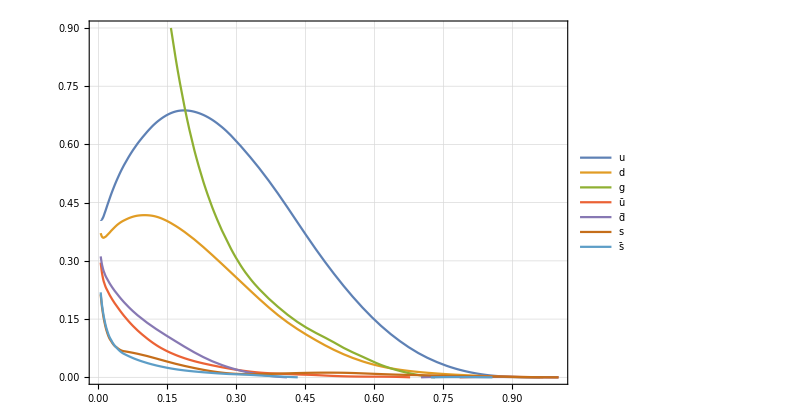

```mathematica
(* Plot xPDF : Peskin pg 563 *)
uppdf=xPDFcv[x,4,2];  (* Peak height is different from the Peskin *)
downpdf=xPDFcv[x,4,1];
gluepdf=xPDFcv[x,4,0];
upbarpdf=xPDFcv[x,4,-2];
dbarpdf=xPDFcv[x,4,-1];
spdf=xPDFcv[x,4,3];
sbarpdf=xPDFcv[x,4,-3];   
Plot[{uppdf,downpdf,gluepdf,upbarpdf,dbarpdf,spdf,sbarpdf},{x,0.005,1},PlotRange->{{0,1},{0,0.9}},PlotLegends->{"u","d","g","ū","d̄","s","s̄"}]
```

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0,    3 (strange),  4(charm)  *)

uubarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-2]+pdf[M/(√scoll)Exp[Y],-2]pdf[M/(√scoll)Exp[-Y], 2]);
ddbarpdf=2/M(pdf[M/(√scoll)Exp[Y],1]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 1]);ssbarpdf=2/M(pdf[M/(√scoll)Exp[Y],3]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 3]);
ccbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-4]+pdf[M/(√scoll)Exp[Y],-4]pdf[M/(√scoll)Exp[-Y], 4]);
```

### Proton Level Calculation

#### dσ/dM Calculation

```mathematica
dσdCθuubar = dσuu2lldCθ;
dσdCθddbar = dσdd2lldCθ;
partonicσuubar[n_]:=Integrate[SeriesCoefficient[dσdCθuubar,{x,0,n}],{Cθ,-1,1}]/.{Ein->M/2}//Simplify
partonicσddbar[n_]:=Integrate[SeriesCoefficient[dσdCθddbar,{x,0,n}],{Cθ,-1,1}]/.{Ein->M/2}//Simplify
```

```mathematica
variableSMuubar=partonicσuubar[0];
variableSMddbar=partonicσddbar[0];
variableOxuubar=partonicσuubar[1];
variableOxddbar=partonicσddbar[1];
variableOx2uubar=partonicσuubar[2];
variableOx2ddbar=partonicσddbar[2];
```

```mathematica
σpp2lνSMuu=1/10^5 Vegas[10^5 (variableSMuubar uubarpdf),{M,2000,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
σpp2lνSMdd=1/10^5 Vegas[10^5 (variableSMddbar ddbarpdf),{M,2000,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
```

Vegas::success: Needed 450000 function evaluations.

(0.000208319 | 1.54116×10^-7 | 3.80988×10^-9)

Vegas::success: Needed 450000 function evaluations.

(0.0000510194 | 3.85582×10^-8 | 2.78887×10^-9)

```mathematica
σpp2lνSMss=1/10^5 Vegas[10^5 (variableSMuubar ssbarpdf),{M,2000,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
σpp2lνSMcc=1/10^5 Vegas[10^5 (variableSMddbar ccbarpdf),{M,2000,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
```

Vegas::success: Needed 450000 function evaluations.

(4.89227×10^-6 | 3.74931×10^-9 | 3.00765×10^-9)

Vegas::success: Needed 100000 function evaluations.

(4.60078×10^-7 | 9.01616×10^-9 | -0.00999)

```mathematica
variablelistOxuubar = DeleteDuplicates@Cases[variableOxuubar//N,_Symbol,Infinity]
variablelistOxuubar=Delete[variablelistOxuubar,{{1}}]
dσdMOxuubarterm=Table[Coefficient[variableOxuubar,variablelistOxuubar[[wilson]]],{wilson,1,Length[variablelistOxuubar]}];

variablelistOxddbar = DeleteDuplicates@Cases[variableOxddbar//N,_Symbol,Infinity]
variablelistOxddbar=Delete[variablelistOxddbar,{{1}}]
dσdMOxddbarterm=Table[Coefficient[variableOxddbar,variablelistOxddbar[[wilson]]],{wilson,1,Length[variablelistOxddbar]}];
```

{M,δGF6,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,CeQ6til,Ceu6til,CLQ36til,CLQ6til,CLu6til}

{δGF6,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,CeQ6til,Ceu6til,CLQ36til,CLQ6til,CLu6til}

{M,δGF6,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,Ced6til,CeQ6til,CLd6til,CLQ36til,CLQ6til}

{δGF6,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,Ced6til,CeQ6til,CLd6til,CLQ36til,CLQ6til}

```mathematica
σpp2lνOxuubar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOxuubarterm[[i]]uubarpdf,{M,2000,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOxuubar,{ variablelistOxuubar[[i]],protonσ}],{i,1,Length[variablelistOxuubar]}],i];
σpp2lνOxuubar
```

Vegas::success: Needed 450000 function evaluations.

Vegas::success: Needed 100000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

(δGF6 | (-0.000589216 | 4.35906×10^-7 | 3.80988×10^-9)
CHD6til | (-0.000413828 | 3.06337×10^-7 | 3.81005×10^-9)
CHdc16til | (3.90123×10^-14 | 7.20695×10^-16 | -0.00999)
CHec16til | (-0.0000254574 | 1.87955×10^-8 | 3.82248×10^-9)
CHL16til | (0.00017914 | 1.32449×10^-7 | 3.81543×10^-9)
CHL36til | (0.00017914 | 1.32449×10^-7 | 3.81543×10^-9)
CHQ16til | (-0.000142523 | 1.05363×10^-7 | 3.81597×10^-9)
CHQ36til | (0.000142523 | 1.05363×10^-7 | 3.81597×10^-9)
CHuc16til | (0.0000352274 | 2.60341×10^-8 | 3.81738×10^-9)
CHWB6til | (-0.000955383 | 7.07211×10^-7 | 3.81016×10^-9)
CeQ6til | (-0.0372399 | 0.0000256602 | 6.69522×10^-9)
Ceu6til | (-0.149446 | 0.000102942 | 6.65819×10^-9)
CLQ36til | (0.0535446 | 0.0000368818 | 6.65884×10^-9)
CLQ6til | (-0.214178 | 0.000147527 | 6.65884×10^-9)
CLu6til | (-0.0746418 | 0.000051421 | 6.65597×10^-9))

```mathematica
int1uu=Table[σpp2lνOxuubar[[i,2,1,1]],{i,1,Length[σpp2lνOxuubar]}];
taeOxuuResult=variablelistOxuubar.int1uu
```

-0.0372399 CeQ6til-0.149446 Ceu6til-0.000413828 CHD6til+3.90123×10^-14 CHdc16til-0.0000254574 CHec16til+0.00017914 CHL16til+0.00017914 CHL36til-0.000142523 CHQ16til+0.000142523 CHQ36til+0.0000352274 CHuc16til-0.000955383 CHWB6til+0.0535446 CLQ36til-0.214178 CLQ6til-0.0746418 CLu6til-0.000589216 δGF6

```mathematica
σpp2lνOxddbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOxddbarterm[[i]]ddbarpdf,{M,2000,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOxddbar,{ variablelistOxddbar[[i]],protonσ}],{i,1,Length[variablelistOxddbar]}],i];
σpp2lνOxddbar
```

Vegas::success: Needed 450000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

(δGF6 | (-0.000144305 | 1.09059×10^-7 | 2.78887×10^-9)
CHD6til | (-0.0000292202 | 2.21143×10^-8 | 2.77521×10^-9)
CHdc16til | (-8.17513×10^-6 | 6.17353×10^-9 | 2.79674×10^-9)
CHec16til | (-0.00002787 | 2.10404×10^-8 | 2.7996×10^-9)
CHL16til | (0.0000939474 | 7.09806×10^-8 | 2.79177×10^-9)
CHL36til | (0.0000939474 | 7.09806×10^-8 | 2.79177×10^-9)
CHQ16til | (0.0000743234 | 5.61458×10^-8 | 2.79321×10^-9)
CHQ36til | (0.0000743234 | 5.61458×10^-8 | 2.79321×10^-9)
CHuc16til | (-3.10709×10^-14 | 6.52015×10^-16 | -0.00999)
CHWB6til | (-0.0000668652 | 5.06201×10^-8 | 2.77227×10^-9)
Ced6til | (0.0329045 | 0.0000238694 | 1.01126×10^-9)
CeQ6til | (-0.0165087 | 0.0000119874 | 9.89115×10^-10)
CLd6til | (0.0164335 | 0.0000119227 | 1.01121×10^-9)
CLQ36til | (0.0194706 | 0.0000141524 | 9.86707×10^-10)
CLQ6til | (0.0778826 | 0.0000566096 | 9.86707×10^-10))

```mathematica
int1dd=Table[σpp2lνOxddbar[[i,2,1,1]],{i,1,Length[σpp2lνOxddbar]}];
taeOxddResult=variablelistOxddbar.int1dd
```

0.0329045 Ced6til-0.0165087 CeQ6til-0.0000292202 CHD6til-8.17513×10^-6 CHdc16til-0.00002787 CHec16til+0.0000939474 CHL16til+0.0000939474 CHL36til+0.0000743234 CHQ16til+0.0000743234 CHQ36til-3.10709×10^-14 CHuc16til-0.0000668652 CHWB6til+0.0164335 CLd6til+0.0194706 CLQ36til+0.0778826 CLQ6til-0.000144305 δGF6

```mathematica
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_uubarOx_M2000.txt",taeOxuuResult];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ddbarOx_M2000.txt",taeOxddResult];
```

```mathematica
variablelistOx2uubar={δGF6^2, CHD6til δGF6, CHdc16til δGF6, CHec16til δGF6, CHL16til δGF6,CHL36til δGF6, CHQ16til δGF6,CHQ36til δGF6,CHuc16til δGF6,CHWB6til δGF6,CeQ6til δGF6,Ceu6til δGF6, CLQ36til δGF6, CLQ6til δGF6, CLu6til δGF6, CHD6til^2, CHD6til CHdc16til,CHD6til CHec16til,CHD6til CHL16til,CHD6til CHL36til, CHD6til CHQ16til,CHD6til CHQ36til,CHD6til CHuc16til,CHD6til CHWB6til,CeQ6til CHD6til,Ceu6til CHD6til,CHD6til CLQ36til,CHD6til CLQ6til,CHD6til CLu6til,CHdc16til^2, CHdc16til CHec16til, CHdc16til CHL16til,CHdc16til CHL36til,CHdc16til CHQ16til,CHdc16til CHQ36til, CHdc16til CHuc16til, CHdc16til CHWB6til, CeQ6til CHdc16til, Ceu6til CHdc16til, CHdc16til CLQ36til, CHdc16til CLQ6til, CHdc16til CLu6til, CHec16til^2, CHec16til CHL16til, CHec16til CHL36til, CHec16til CHQ16til, CHec16til CHQ36til, CHec16til CHuc16til, CHec16til CHWB6til, CeQ6til CHec16til, Ceu6til CHec16til, CHec16til CLQ36til, CHec16til CLQ6til, CHec16til CLu6til, CHL16til^2, CHL16til CHL36til, CHL16til CHQ16til, CHL16til CHQ36til, CHL16til CHuc16til, CHL16til CHWB6til, CeQ6til CHL16til, Ceu6til CHL16til, CHL16til CLQ36til, CHL16til CLQ6til, CHL16til CLu6til, CHL36til^2, CHL36til CHQ16til, CHL36til CHQ36til, CHL36til CHuc16til, CHL36til CHWB6til, CeQ6til CHL36til, Ceu6til CHL36til, CHL36til CLQ36til, CHL36til CLQ6til, CHL36til CLu6til, CHQ16til^2, CHQ16til CHQ36til, CHQ16til CHuc16til, CHQ16til CHWB6til, CeQ6til CHQ16til, Ceu6til CHQ16til, CHQ16til CLQ36til, CHQ16til CLQ6til, CHQ16til CLu6til, CHQ36til^2, CHQ36til CHuc16til, CHQ36til CHWB6til, CeQ6til CHQ36til, Ceu6til CHQ36til, CHQ36til CLQ36til, CHQ36til CLQ6til, CHQ36til CLu6til, CHuc16til^2, CHuc16til CHWB6til, CeQ6til CHuc16til, Ceu6til CHuc16til, CHuc16til CLQ36til, CHuc16til CLQ6til, CHuc16til CLu6til, CHWB6til^2, CeQ6til CHWB6til, Ceu6til CHWB6til, CHWB6til CLQ36til, CHWB6til CLQ6til, CHWB6til CLu6til, CHB6til CHWB6til, CHW6til CHWB6til, CeQ6til^2, Ceu6til^2, CLQ36til^2, CLQ36til CLQ6til, CLQ6til^2, CLu6til^2, δGF8, CHD28til, CHD8til, CHdc18til, CHec18til, CHL18til, CHL28til, CHL38til, CHQ18til, CHQ28til, CHQ38til,CHuc18til, CHW28til, CHWB8til, CeQs8til, CeQt8til, Ceus8til, Ceut8til, CHeQ18til, CHeQ38til, CHeu8til, CHLQ18til, CHLQ28til, CHLQ38til, CHLQ48til, CHLu18til, CHLu38til, CLQs18til, CLQs38til, CLQt18til, CLQt38til, CLus8til, CLut8til};

dσdMOx2uubarterm=Table[Coefficient[variableOx2uubar,variablelistOx2uubar[[wilson]]],{wilson,1,Length[variablelistOx2uubar]}];
```

```mathematica
(*1/10^5 Vegas[10^5 dσdMOx2uubarterm[[2]] uubarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]*)
```

```mathematica
σpp2lνOx2uubar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOx2uubarterm[[i]]uubarpdf,{M,2000,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOx2uubar,{ variablelistOx2uubar[[i]],protonσ}],{i,1,Length[variablelistOx2uubar]}],i];
σpp2lνOx2uubar
```

Vegas::success: Needed 450000 function evaluations.

Vegas::success: Needed 100000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

(δGF6^2 | (0.00124992 | 9.24697×10^-7 | 3.80988×10^-9)
CHD6til δGF6 | (0.00117048 | 8.66451×10^-7 | 3.81005×10^-9)
CHdc16til δGF6 | (-2.20687×10^-13 | 4.07686×10^-15 | -0.00999)
CHec16til δGF6 | (0.0000720044 | 5.31617×10^-8 | 3.82248×10^-9)
CHL16til δGF6 | (-0.000506684 | 3.74622×10^-7 | 3.81543×10^-9)
CHL36til δGF6 | (-0.000506684 | 3.74622×10^-7 | 3.81543×10^-9)
CHQ16til δGF6 | (0.000403117 | 2.98011×10^-7 | 3.81597×10^-9)
CHQ36til δGF6 | (-0.000403117 | 2.98011×10^-7 | 3.81597×10^-9)
CHuc16til δGF6 | (-0.000099638 | 7.36355×10^-8 | 3.81738×10^-9)
CHWB6til δGF6 | (0.00270223 | 2.0003×10^-6 | 3.81016×10^-9)
CeQ6til δGF6 | (0.10533 | 0.0000725781 | 6.69522×10^-9)
Ceu6til δGF6 | (0.422696 | 0.000291165 | 6.65819×10^-9)
CLQ36til δGF6 | (-0.151447 | 0.000104318 | 6.65884×10^-9)
CLQ6til δGF6 | (0.605788 | 0.00041727 | 6.65884×10^-9)
CLu6til δGF6 | (0.211119 | 0.00014544 | 6.65597×10^-9)
CHD6til^2 | (0.000621037 | 4.59446×10^-7 | 3.80989×10^-9)
CHD6til CHdc16til | (-1.92914×10^-14 | 3.56575×10^-16 | -0.00999)
CHD6til CHec16til | (0.000204763 | 1.51373×10^-7 | 3.81603×10^-9)
CHD6til CHL16til | (0.000147875 | 1.0932×10^-7 | 3.81594×10^-9)
CHD6til CHL36til | (0.000147875 | 1.0932×10^-7 | 3.81594×10^-9)
CHD6til CHQ16til | (-0.000221197 | 1.63595×10^-7 | 3.81409×10^-9)
CHD6til CHQ36til | (0.000221197 | 1.63595×10^-7 | 3.81409×10^-9)
CHD6til CHuc16til | (-0.000339659 | 2.51164×10^-7 | 3.81485×10^-9)
CHD6til CHWB6til | (0.00270858 | 2.00425×10^-6 | 3.80898×10^-9)
CeQ6til CHD6til | (0.0836316 | 0.0000576207 | 6.69684×10^-9)
Ceu6til CHD6til | (0.335374 | 0.000231009 | 6.65867×10^-9)
CHD6til CLQ36til | (-0.0104186 | 7.18082×10^-6 | 6.69111×10^-9)
CHD6til CLQ6til | (0.0416745 | 0.0000287233 | 6.69111×10^-9)
CHD6til CLu6til | (0.167546 | 0.000115417 | 6.65696×10^-9)
CHdc16til^2 | (-1.34831×10^-13 | 2.4908×10^-15 | -0.00999)
CHdc16til CHec16til | (-2.39535×10^-14 | 4.42651×10^-16 | -0.00999)
CHdc16til CHL16til | (1.1159×10^-13 | 2.06136×10^-15 | -0.00999)
CHdc16til CHL36til | (1.43362×10^-13 | 2.64831×10^-15 | -0.00999)
CHdc16til CHQ16til | (-7.61717×10^-14 | 1.40716×10^-15 | -0.00999)
CHdc16til CHQ36til | (1.57327×10^-13 | 2.90638×10^-15 | -0.00999)
CHdc16til CHuc16til | (3.27807×10^-14 | 6.05621×10^-16 | -0.00999)
CHdc16til CHWB6til | (5.15452×10^-14 | 9.52047×10^-16 | -0.00999)
CeQ6til CHdc16til | (4.43274×10^-11 | 7.24245×10^-13 | -0.00999)
Ceu6til CHdc16til | (-1.87402×10^-11 | 3.06188×10^-13 | -0.00999)
CHdc16til CLQ36til | (1.37811×10^-11 | 2.25163×10^-13 | -0.00999)
CHdc16til CLQ6til | (-5.51244×10^-11 | 9.00654×10^-13 | -0.00999)
CHdc16til CLu6til | (2.33048×10^-11 | 3.80768×10^-13 | -0.00999)
CHec16til^2 | (0.000102299 | 7.56212×10^-8 | 3.81625×10^-9)
CHec16til CHL16til | (9.4717×10^-14 | 1.74952×10^-15 | -0.00999)
CHec16til CHL36til | (2.022×10^-13 | 3.73576×10^-15 | -0.00999)
CHec16til CHQ16til | (0.0000581198 | 4.29063×10^-8 | 3.82294×10^-9)
CHec16til CHQ36til | (-0.0000581198 | 4.29063×10^-8 | 3.82294×10^-9)
CHec16til CHuc16til | (-0.000255094 | 1.88633×10^-7 | 3.81482×10^-9)
CHec16til CHWB6til | (0.0000340842 | 2.51711×10^-8 | 3.82059×10^-9)
CeQ6til CHec16til | (-0.176938 | 0.000121867 | 6.66034×10^-9)
Ceu6til CHec16til | (0.0748039 | 0.0000515216 | 6.66034×10^-9)
CHec16til CLQ36til | (1.37811×10^-11 | 2.25163×10^-13 | -0.00999)
CHec16til CLQ6til | (-5.51244×10^-11 | 9.00654×10^-13 | -0.00999)
CHec16til CLu6til | (2.33048×10^-11 | 3.80768×10^-13 | -0.00999)
CHL16til^2 | (0.000102299 | 7.56212×10^-8 | 3.81625×10^-9)
CHL16til CHL36til | (0.000204597 | 1.51242×10^-7 | 3.81625×10^-9)
CHL16til CHQ16til | (-0.000435791 | 3.22207×10^-7 | 3.81542×10^-9)
CHL16til CHQ36til | (0.000435791 | 3.22207×10^-7 | 3.81542×10^-9)
CHL16til CHuc16til | (-0.0000462845 | 3.40568×10^-8 | 3.80472×10^-9)
CHL16til CHWB6til | (0.000192283 | 1.42114×10^-7 | 3.81702×10^-9)
CeQ6til CHL16til | (4.43274×10^-11 | 7.24245×10^-13 | -0.00999)
Ceu6til CHL16til | (-1.87402×10^-11 | 3.06188×10^-13 | -0.00999)
CHL16til CLQ36til | (0.0442346 | 0.0000304668 | 6.66034×10^-9)
CHL16til CLQ6til | (-0.176938 | 0.000121867 | 6.66034×10^-9)
CHL16til CLu6til | (0.0748039 | 0.0000515216 | 6.66034×10^-9)
CHL36til^2 | (0.000102299 | 7.56212×10^-8 | 3.81625×10^-9)
CHL36til CHQ16til | (-0.000435791 | 3.22207×10^-7 | 3.81542×10^-9)
CHL36til CHQ36til | (0.000435791 | 3.22207×10^-7 | 3.81542×10^-9)
CHL36til CHuc16til | (-0.0000462845 | 3.40568×10^-8 | 3.80472×10^-9)
CHL36til CHWB6til | (0.000192283 | 1.42114×10^-7 | 3.81702×10^-9)
CeQ6til CHL36til | (-1.54576×10^-10 | 2.52555×10^-12 | -0.00999)
Ceu6til CHL36til | (6.53499×10^-11 | 1.06772×10^-12 | -0.00999)
CHL36til CLQ36til | (0.0442346 | 0.0000304668 | 6.66034×10^-9)
CHL36til CLQ6til | (-0.176938 | 0.000121867 | 6.66034×10^-9)
CHL36til CLu6til | (0.0748039 | 0.0000515216 | 6.66034×10^-9)
CHQ16til^2 | (0.0000888753 | 6.56985×10^-8 | 3.81625×10^-9)
CHQ16til CHQ36til | (-0.000177751 | 1.31397×10^-7 | 3.81625×10^-9)
CHQ16til CHuc16til | (4.14179×10^-14 | 7.65015×10^-16 | -0.00999)
CHQ16til CHWB6til | (-0.000347281 | 2.56796×10^-7 | 3.81493×10^-9)
CeQ6til CHQ16til | (-0.112206 | 0.0000772824 | 6.66034×10^-9)
Ceu6til CHQ16til | (4.82918×10^-11 | 7.89018×10^-13 | -0.00999)
CHQ16til CLQ36til | (-0.0348841 | 0.0000240266 | 6.66034×10^-9)
CHQ16til CLQ6til | (0.139536 | 0.0000961065 | 6.66034×10^-9)
CHQ16til CLu6til | (-6.00545×10^-11 | 9.81204×10^-13 | -0.00999)
CHQ36til^2 | (0.0000888753 | 6.56985×10^-8 | 3.81625×10^-9)
CHQ36til CHuc16til | (-4.17132×10^-13 | 7.70631×10^-15 | -0.00999)
CHQ36til CHWB6til | (0.000347281 | 2.56796×10^-7 | 3.81493×10^-9)
CeQ6til CHQ36til | (0.112206 | 0.0000772824 | 6.66034×10^-9)
Ceu6til CHQ36til | (1.66498×10^-10 | 2.72034×10^-12 | -0.00999)
CHQ36til CLQ36til | (0.0348841 | 0.0000240266 | 6.66034×10^-9)
CHQ36til CLQ6til | (-0.139536 | 0.0000961065 | 6.66034×10^-9)
CHQ36til CLu6til | (-2.07053×10^-10 | 3.38295×10^-12 | -0.00999)
CHuc16til^2 | (0.0000888753 | 6.56985×10^-8 | 3.81625×10^-9)
CHuc16til CHWB6til | (-0.000283782 | 2.09856×10^-7 | 3.81464×10^-9)
CeQ6til CHuc16til | (-5.91032×10^-11 | 9.65661×10^-13 | -0.00999)
Ceu6til CHuc16til | (-0.112206 | 0.0000772824 | 6.66034×10^-9)
CHuc16til CLQ36til | (-1.83748×10^-11 | 3.00218×10^-13 | -0.00999)
CHuc16til CLQ6til | (7.34992×10^-11 | 1.20087×10^-12 | -0.00999)
CHuc16til CLu6til | (0.139536 | 0.0000961065 | 6.66034×10^-9)
CHWB6til^2 | (0.0031799 | 2.35308×10^-6 | 3.80886×10^-9)
CeQ6til CHWB6til | (0.348615 | 0.000240151 | 6.65685×10^-9)
Ceu6til CHWB6til | (0.558147 | 0.000384468 | 6.65819×10^-9)
CHWB6til CLQ36til | (-0.0522318 | 0.0000359852 | 6.65447×10^-9)
CHWB6til CLQ6til | (0.208927 | 0.000143941 | 6.65447×10^-9)
CHWB6til CLu6til | (0.418459 | 0.000288257 | 6.65745×10^-9)
CHB6til CHWB6til | (-0.000955383 | 7.07211×10^-7 | 3.81016×10^-9)
CHW6til CHWB6til | (-0.000955383 | 7.07211×10^-7 | 3.81016×10^-9)
CeQ6til^2 | (106.498 | 0.0699655 | 4.10418×10^-9)
Ceu6til^2 | (106.498 | 0.0699655 | 4.10418×10^-9)
CLQ36til^2 | (6.65615 | 0.00437284 | 4.10418×10^-9)
CLQ36til CLQ6til | (-53.2492 | 0.0349827 | 4.10418×10^-9)
CLQ6til^2 | (106.498 | 0.0699655 | 4.10418×10^-9)
CLu6til^2 | (106.498 | 0.0699655 | 4.10418×10^-9)
δGF8 | (-0.000589216 | 4.35906×10^-7 | 3.80988×10^-9)
CHD28til | (-0.000309668 | 2.29262×10^-7 | 3.80925×10^-9)
CHD8til | (-0.00010416 | 7.70581×10^-8 | 3.80988×10^-9)
CHdc18til | (1.95061×10^-14 | 3.60347×10^-16 | -0.00999)
CHec18til | (-0.0000127287 | 9.39776×10^-9 | 3.82248×10^-9)
CHL18til | (0.0000895699 | 6.62245×10^-8 | 3.81543×10^-9)
CHL28til | (0.0000895699 | 6.62245×10^-8 | 3.81543×10^-9)
CHL38til | (0.0000895699 | 6.62245×10^-8 | 3.81543×10^-9)
CHQ18til | (-0.0000712617 | 5.26814×10^-8 | 3.81597×10^-9)
CHQ28til | (0.0000712617 | 5.26814×10^-8 | 3.81597×10^-9)
CHQ38til | (0.0000712617 | 5.26814×10^-8 | 3.81597×10^-9)
CHuc18til | (0.0000176137 | 1.3017×10^-8 | 3.81738×10^-9)
CHW28til | (-0.000411014 | 3.02715×10^-7 | 3.75794×10^-9)
CHWB8til | (-14.4798 | 0.0107185 | 3.81016×10^-9)
CeQs8til | (2.16483 | 0.00142221 | 4.10192×10^-9)
CeQt8til | (-1.62362 | 0.00106666 | 4.10192×10^-9)
Ceus8til | (8.68324 | 0.00570456 | 4.10444×10^-9)
Ceut8til | (-2.17081 | 0.00142614 | 4.10444×10^-9)
CHeQ18til | (-0.01862 | 0.0000128301 | 6.69522×10^-9)
CHeQ38til | (0.00465499 | 3.20753×10^-6 | 6.69522×10^-9)
CHeu8til | (-0.0747229 | 0.0000514712 | 6.65819×10^-9)
CHLQ18til | (-0.107089 | 0.0000737636 | 6.65884×10^-9)
CHLQ28til | (0.0267723 | 0.0000184409 | 6.65884×10^-9)
CHLQ38til | (-0.0267723 | 0.0000184409 | 6.65884×10^-9)
CHLQ48til | (0.0267723 | 0.0000184409 | 6.65884×10^-9)
CHLu18til | (-0.0373209 | 0.0000257105 | 6.65597×10^-9)
CHLu38til | (-0.00933023 | 6.42762×10^-6 | 6.65597×10^-9)
CLQs18til | (12.4438 | 0.0081751 | 4.10473×10^-9)
CLQs38til | (-3.11094 | 0.00204377 | 4.10473×10^-9)
CLQt18til | (-3.11094 | 0.00204377 | 4.10473×10^-9)
CLQt38til | (0.777735 | 0.000510943 | 4.10473×10^-9)
CLus8til | (4.33763 | 0.00284966 | 4.10353×10^-9)
CLut8til | (-3.25322 | 0.00213724 | 4.10353×10^-9))

```mathematica
variablelistOx2ddbar={δGF6^2,CHD6til δGF6, CHdc16til δGF6,CHec16til δGF6,CHL16til δGF6, CHL36til δGF6, CHQ16til δGF6, CHQ36til δGF6, CHuc16til δGF6, CHWB6til δGF6, Ced6til δGF6, CeQ6til δGF6, CLd6til δGF6, CLQ36til δGF6, CLQ6til δGF6, CHD6til^2, CHD6til CHdc16til, CHD6til CHec16til, CHD6til CHL16til, CHD6til CHL36til, CHD6til CHQ16til, CHD6til CHQ36til, CHD6til CHuc16til, CHD6til CHWB6til, Ced6til CHD6til, CeQ6til CHD6til, CHD6til CLd6til, CHD6til CLQ36til, CHD6til CLQ6til, CHdc16til^2, CHdc16til CHec16til, CHdc16til CHL16til, CHdc16til CHL36til, CHdc16til CHQ16til, CHdc16til CHQ36til, CHdc16til CHuc16til, CHdc16til CHWB6til, Ced6til CHdc16til, CeQ6til CHdc16til, CHdc16til CLd6til, CHdc16til CLQ36til, CHdc16til CLQ6til, CHec16til^2, CHec16til CHL16til, CHec16til CHL36til, CHec16til CHQ16til, CHec16til CHQ36til, CHec16til CHuc16til, CHec16til CHWB6til, Ced6til CHec16til, CeQ6til CHec16til, CHec16til CLd6til, CHec16til CLQ36til, CHec16til CLQ6til, CHL16til^2, CHL16til CHL36til, CHL16til CHQ16til, CHL16til CHQ36til, CHL16til CHuc16til, CHL16til CHWB6til, Ced6til CHL16til, CeQ6til CHL16til, CHL16til CLd6til, CHL16til CLQ36til, CHL16til CLQ6til, CHL36til^2, CHL36til CHQ16til, CHL36til CHQ36til, CHL36til CHuc16til, CHL36til CHWB6til, Ced6til CHL36til, CeQ6til CHL36til, CHL36til CLd6til, CHL36til CLQ36til, CHL36til CLQ6til, CHQ16til^2, CHQ16til CHQ36til, CHQ16til CHuc16til, CHQ16til CHWB6til, Ced6til CHQ16til, CeQ6til CHQ16til, CHQ16til CLd6til, CHQ16til CLQ36til, CHQ16til CLQ6til, CHQ36til^2, CHQ36til CHuc16til, CHQ36til CHWB6til, Ced6til CHQ36til, CeQ6til CHQ36til, CHQ36til CLd6til, CHQ36til CLQ36til, CHQ36til CLQ6til, CHuc16til^2, CHuc16til CHWB6til, Ced6til CHuc16til, CeQ6til CHuc16til, CHuc16til CLd6til, CHuc16til CLQ36til, CHuc16til CLQ6til, CHWB6til^2, Ced6til CHWB6til, CeQ6til CHWB6til, CHWB6til CLd6til, CHWB6til CLQ36til, CHWB6til CLQ6til, CHB6til CHWB6til, CHW6til CHWB6til, Ced6til^2, CeQ6til^2, CLd6til^2, CLQ36til^2, CLQ36til CLQ6til, CLQ6til^2, δGF8, CHD28til, CHD8til, CHdc18til, CHec18til, CHL18til, CHL28til, CHL38til, CHQ18til, CHQ28til, CHQ38til, CHuc18til, CHW28til, CHWB8til, Ceds8til, Cedt8til, CeQs8til, CeQt8til, CHed8til, CHeQ18til, CHeQ38til, CHLd18til, CHLd38til, CHLQ18til, CHLQ28til, CHLQ38til, CHLQ48til, CLds8til, CLdt8til, CLQs18til, CLQs38til, CLQt18til, CLQt38til}

dσdMOx2ddbarterm=Table[Coefficient[variableOx2ddbar,variablelistOx2ddbar[[wilson]]],{wilson,1,Length[variablelistOx2ddbar]}];
```

{δGF6^2,CHD6til δGF6,CHdc16til δGF6,CHec16til δGF6,CHL16til δGF6,CHL36til δGF6,CHQ16til δGF6,CHQ36til δGF6,CHuc16til δGF6,CHWB6til δGF6,Ced6til δGF6,CeQ6til δGF6,CLd6til δGF6,CLQ36til δGF6,CLQ6til δGF6,CHD6til^2,CHD6til CHdc16til,CHD6til CHec16til,CHD6til CHL16til,CHD6til CHL36til,CHD6til CHQ16til,CHD6til CHQ36til,CHD6til CHuc16til,CHD6til CHWB6til,Ced6til CHD6til,CeQ6til CHD6til,CHD6til CLd6til,CHD6til CLQ36til,CHD6til CLQ6til,CHdc16til^2,CHdc16til CHec16til,CHdc16til CHL16til,CHdc16til CHL36til,CHdc16til CHQ16til,CHdc16til CHQ36til,CHdc16til CHuc16til,CHdc16til CHWB6til,Ced6til CHdc16til,CeQ6til CHdc16til,CHdc16til CLd6til,CHdc16til CLQ36til,CHdc16til CLQ6til,CHec16til^2,CHec16til CHL16til,CHec16til CHL36til,CHec16til CHQ16til,CHec16til CHQ36til,CHec16til CHuc16til,CHec16til CHWB6til,Ced6til CHec16til,CeQ6til CHec16til,CHec16til CLd6til,CHec16til CLQ36til,CHec16til CLQ6til,CHL16til^2,CHL16til CHL36til,CHL16til CHQ16til,CHL16til CHQ36til,CHL16til CHuc16til,CHL16til CHWB6til,Ced6til CHL16til,CeQ6til CHL16til,CHL16til CLd6til,CHL16til CLQ36til,CHL16til CLQ6til,CHL36til^2,CHL36til CHQ16til,CHL36til CHQ36til,CHL36til CHuc16til,CHL36til CHWB6til,Ced6til CHL36til,CeQ6til CHL36til,CHL36til CLd6til,CHL36til CLQ36til,CHL36til CLQ6til,CHQ16til^2,CHQ16til CHQ36til,CHQ16til CHuc16til,CHQ16til CHWB6til,Ced6til CHQ16til,CeQ6til CHQ16til,CHQ16til CLd6til,CHQ16til CLQ36til,CHQ16til CLQ6til,CHQ36til^2,CHQ36til CHuc16til,CHQ36til CHWB6til,Ced6til CHQ36til,CeQ6til CHQ36til,CHQ36til CLd6til,CHQ36til CLQ36til,CHQ36til CLQ6til,CHuc16til^2,CHuc16til CHWB6til,Ced6til CHuc16til,CeQ6til CHuc16til,CHuc16til CLd6til,CHuc16til CLQ36til,CHuc16til CLQ6til,CHWB6til^2,Ced6til CHWB6til,CeQ6til CHWB6til,CHWB6til CLd6til,CHWB6til CLQ36til,CHWB6til CLQ6til,CHB6til CHWB6til,CHW6til CHWB6til,Ced6til^2,CeQ6til^2,CLd6til^2,CLQ36til^2,CLQ36til CLQ6til,CLQ6til^2,δGF8,CHD28til,CHD8til,CHdc18til,CHec18til,CHL18til,CHL28til,CHL38til,CHQ18til,CHQ28til,CHQ38til,CHuc18til,CHW28til,CHWB8til,Ceds8til,Cedt8til,CeQs8til,CeQt8til,CHed8til,CHeQ18til,CHeQ38til,CHLd18til,CHLd38til,CHLQ18til,CHLQ28til,CHLQ38til,CHLQ48til,CLds8til,CLdt8til,CLQs18til,CLQs38til,CLQt18til,CLQt38til}

```mathematica
σpp2lνOx2ddbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOx2ddbarterm[[i]]ddbarpdf,{M,2000,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOx2ddbar,{ variablelistOx2ddbar[[i]],protonσ}],{i,1,Length[variablelistOx2ddbar]}],i];
σpp2lνOx2ddbar
```

Vegas::success: Needed 450000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

(δGF6^2 | (0.000306116 | 2.31349×10^-7 | 2.78887×10^-9)
CHD6til δGF6 | (0.0000826471 | 6.25486×10^-8 | 2.77521×10^-9)
CHdc16til δGF6 | (0.0000231228 | 1.74614×10^-8 | 2.79674×10^-9)
CHec16til δGF6 | (0.0000788284 | 5.95112×10^-8 | 2.7996×10^-9)
CHL16til δGF6 | (-0.000265723 | 2.00763×10^-7 | 2.79177×10^-9)
CHL36til δGF6 | (-0.000265723 | 2.00763×10^-7 | 2.79177×10^-9)
CHQ16til δGF6 | (-0.000210218 | 1.58804×10^-7 | 2.79321×10^-9)
CHQ36til δGF6 | (-0.000210218 | 1.58804×10^-7 | 2.79321×10^-9)
CHuc16til δGF6 | (1.75763×10^-13 | 3.68835×10^-15 | -0.00999)
CHWB6til δGF6 | (0.000189123 | 1.43175×10^-7 | 2.77227×10^-9)
Ced6til δGF6 | (-0.093068 | 0.0000675128 | 1.01126×10^-9)
CeQ6til δGF6 | (0.0466936 | 0.0000339055 | 9.89115×10^-10)
CLd6til δGF6 | (-0.0464808 | 0.0000337226 | 1.01121×10^-9)
CLQ36til δGF6 | (-0.0550713 | 0.000040029 | 9.86707×10^-10)
CLQ6til δGF6 | (-0.220285 | 0.000160116 | 9.86707×10^-10)
CHD6til^2 | (0.0000712334 | 5.383×10^-8 | 2.7898×10^-9)
CHD6til CHdc16til | (0.0000788199 | 5.95643×10^-8 | 2.78958×10^-9)
CHD6til CHec16til | (0.000082688 | 6.24434×10^-8 | 2.79663×10^-9)
CHD6til CHL16til | (0.0000202535 | 1.54171×10^-8 | 3.25216×10^-9)
CHD6til CHL36til | (0.0000202535 | 1.54171×10^-8 | 3.25216×10^-9)
CHD6til CHQ16til | (0.0000238389 | 1.8032×10^-8 | 2.7804×10^-9)
CHD6til CHQ36til | (0.0000238389 | 1.8032×10^-8 | 2.7804×10^-9)
CHD6til CHuc16til | (4.31375×10^-14 | 9.05337×10^-16 | -0.00999)
CHD6til CHWB6til | (0.000225591 | 1.70604×10^-7 | 2.78239×10^-9)
Ced6til CHD6til | (-0.0738425 | 0.0000535647 | 1.01127×10^-9)
CeQ6til CHD6til | (0.0370197 | 0.0000269001 | 9.87305×10^-10)
CHD6til CLd6til | (-0.0368885 | 0.0000267615 | 1.01123×10^-9)
CHD6til CLQ36til | (0.00463565 | 3.36505×10^-6 | 9.89827×10^-10)
CHD6til CLQ6til | (0.0185426 | 0.0000134602 | 9.89827×10^-10)
CHdc16til^2 | (0.0000412493 | 3.11597×10^-8 | 2.79356×10^-9)
CHdc16til CHec16til | (0.0000591963 | 4.4735×10^-8 | 2.78951×10^-9)
CHdc16til CHL16til | (0.0000107394 | 8.13108×10^-9 | 2.77126×10^-9)
CHdc16til CHL36til | (0.0000107394 | 8.13108×10^-9 | 2.77126×10^-9)
CHdc16til CHQ16til | (7.68962×10^-14 | 1.61368×10^-15 | -0.00999)
CHdc16til CHQ36til | (1.39253×10^-13 | 2.9223×10^-15 | -0.00999)
CHdc16til CHuc16til | (1.31813×10^-14 | 2.76621×10^-16 | -0.00999)
CHdc16til CHWB6til | (0.0000658531 | 4.97683×10^-8 | 2.78898×10^-9)
Ced6til CHdc16til | (-0.0494132 | 0.0000359141 | 9.86836×10^-10)
CeQ6til CHdc16til | (-2.56165×10^-11 | 4.80584×10^-13 | -0.00999)
CHdc16til CLd6til | (0.0614491 | 0.0000446619 | 9.86836×10^-10)
CHdc16til CLQ36til | (7.96401×10^-12 | 1.4941×10^-13 | -0.00999)
CHdc16til CLQ6til | (3.1856×10^-11 | 5.97642×10^-13 | -0.00999)
CHec16til^2 | (0.0000609087 | 4.60104×10^-8 | 2.79356×10^-9)
CHec16til CHL16til | (4.14814×10^-14 | 8.70367×10^-16 | -0.00999)
CHec16til CHL36til | (1.46994×10^-13 | 3.08483×10^-15 | -0.00999)
CHec16til CHQ16til | (-0.0000861744 | 6.50781×10^-8 | 2.79634×10^-9)
CHec16til CHQ36til | (-0.0000861744 | 6.50781×10^-8 | 2.79634×10^-9)
CHec16til CHuc16til | (3.13525×10^-14 | 6.58016×10^-16 | -0.00999)
CHec16til CHWB6til | (-4.78846×10^-6 | 3.64809×10^-9 | 2.61717×10^-9)
Ced6til CHec16til | (-0.0164711 | 0.0000119714 | 9.86836×10^-10)
CeQ6til CHec16til | (0.0943913 | 0.0000686046 | 9.86836×10^-10)
CHec16til CLd6til | (-5.55881×10^-12 | 1.04287×10^-13 | -0.00999)
CHec16til CLQ36til | (7.96401×10^-12 | 1.4941×10^-13 | -0.00999)
CHec16til CLQ6til | (3.1856×10^-11 | 5.97642×10^-13 | -0.00999)
CHL16til^2 | (0.0000609087 | 4.60104×10^-8 | 2.79356×10^-9)
CHL16til CHL36til | (0.000121817 | 9.20209×10^-8 | 2.79356×10^-9)
CHL16til CHQ16til | (0.000191519 | 1.44691×10^-7 | 2.79231×10^-9)
CHL16til CHQ36til | (0.000191519 | 1.44691×10^-7 | 2.79231×10^-9)
CHL16til CHuc16til | (-8.10217×10^-14 | 1.70016×10^-15 | -0.00999)
CHL16til CHWB6til | (0.0000588115 | 4.43891×10^-8 | 2.80199×10^-9)
Ced6til CHL16til | (4.47002×10^-12 | 8.38608×10^-14 | -0.00999)
CeQ6til CHL16til | (-2.56165×10^-11 | 4.80584×10^-13 | -0.00999)
CHL16til CLd6til | (-0.0164711 | 0.0000119714 | 9.86836×10^-10)
CHL16til CLQ36til | (0.0235978 | 0.0000171512 | 9.86836×10^-10)
CHL16til CLQ6til | (0.0943913 | 0.0000686046 | 9.86836×10^-10)
CHL36til^2 | (0.0000609087 | 4.60104×10^-8 | 2.79356×10^-9)
CHL36til CHQ16til | (0.000191519 | 1.44691×10^-7 | 2.79231×10^-9)
CHL36til CHQ36til | (0.000191519 | 1.44691×10^-7 | 2.79231×10^-9)
CHL36til CHuc16til | (-1.06326×10^-13 | 2.23118×10^-15 | -0.00999)
CHL36til CHWB6til | (0.0000588115 | 4.43891×10^-8 | 2.80199×10^-9)
Ced6til CHL36til | (-1.55876×10^-11 | 2.92435×10^-13 | -0.00999)
CeQ6til CHL36til | (8.93285×10^-11 | 1.67587×10^-12 | -0.00999)
CHL36til CLd6til | (-0.0164711 | 0.0000119714 | 9.86836×10^-10)
CHL36til CLQ36til | (0.0235978 | 0.0000171512 | 9.86836×10^-10)
CHL36til CLQ6til | (0.0943913 | 0.0000686046 | 9.86836×10^-10)
CHQ16til^2 | (0.0000412493 | 3.11597×10^-8 | 2.79356×10^-9)
CHQ16til CHQ36til | (0.0000824986 | 6.23194×10^-8 | 2.79356×10^-9)
CHQ16til CHuc16til | (-8.30934×10^-14 | 1.7437×10^-15 | -0.00999)
CHQ16til CHWB6til | (0.0000953248 | 7.20311×10^-8 | 2.7904×10^-9)
Ced6til CHQ16til | (-1.15188×10^-11 | 2.16102×10^-13 | -0.00999)
CeQ6til CHQ16til | (-0.0494132 | 0.0000359141 | 9.86836×10^-10)
CHQ16til CLd6til | (1.43246×10^-11 | 2.68739×10^-13 | -0.00999)
CHQ16til CLQ36til | (0.0153623 | 0.0000111655 | 9.86836×10^-10)
CHQ16til CLQ6til | (0.0614491 | 0.0000446619 | 9.86836×10^-10)
CHQ36til^2 | (0.0000412493 | 3.11597×10^-8 | 2.79356×10^-9)
CHQ36til CHuc16til | (-1.18664×10^-13 | 2.49015×10^-15 | -0.00999)
CHQ36til CHWB6til | (0.0000953248 | 7.20311×10^-8 | 2.7904×10^-9)
Ced6til CHQ36til | (-3.97141×10^-11 | 7.45065×10^-13 | -0.00999)
CeQ6til CHQ36til | (-0.0494132 | 0.0000359141 | 9.86836×10^-10)
CHQ36til CLd6til | (4.93875×10^-11 | 9.26545×10^-13 | -0.00999)
CHQ36til CLQ36til | (0.0153623 | 0.0000111655 | 9.86836×10^-10)
CHQ36til CLQ6til | (0.0614491 | 0.0000446619 | 9.86836×10^-10)
CHuc16til^2 | (-5.60419×10^-14 | 1.17603×10^-15 | -0.00999)
CHuc16til CHWB6til | (-1.39953×10^-14 | 2.93593×10^-16 | -0.00999)
Ced6til CHuc16til | (-5.96003×10^-12 | 1.11814×10^-13 | -0.00999)
CeQ6til CHuc16til | (3.41553×10^-11 | 6.40778×10^-13 | -0.00999)
CHuc16til CLd6til | (7.41175×10^-12 | 1.3905×10^-13 | -0.00999)
CHuc16til CLQ36til | (-1.06187×10^-11 | 1.99214×10^-13 | -0.00999)
CHuc16til CLQ6til | (-4.24747×10^-11 | 7.96856×10^-13 | -0.00999)
CHWB6til^2 | (0.000331212 | 2.50488×10^-7 | 2.78207×10^-9)
Ced6til CHWB6til | (-0.122891 | 0.000089147 | 1.01126×10^-9)
CeQ6til CHWB6til | (-0.0306174 | 0.0000221844 | 9.61414×10^-10)
CHWB6til CLd6til | (-0.0921333 | 0.0000668379 | 1.01124×10^-9)
CHWB6til CLQ36til | (0.0000351052 | 2.65355×10^-8 | 2.78718×10^-9)
CHWB6til CLQ6til | (0.000140421 | 1.06142×10^-7 | 2.78718×10^-9)
CHB6til CHWB6til | (-0.0000668652 | 5.06201×10^-8 | 2.77227×10^-9)
CHW6til CHWB6til | (-0.0000668652 | 5.06201×10^-8 | 2.77227×10^-9)
Ced6til^2 | (42.1462 | 0.0317664 | 2.92952×10^-9)
CeQ6til^2 | (42.1462 | 0.0317664 | 2.92952×10^-9)
CLd6til^2 | (42.1462 | 0.0317664 | 2.92952×10^-9)
CLQ36til^2 | (2.63413 | 0.0019854 | 2.92952×10^-9)
CLQ36til CLQ6til | (21.0731 | 0.0158832 | 2.92952×10^-9)
CLQ6til^2 | (42.1462 | 0.0317664 | 2.92952×10^-9)
δGF8 | (-0.000144305 | 1.09059×10^-7 | 2.78887×10^-9)
CHD28til | (-3.71063×10^-6 | 8.09963×10^-9 | 8.92009×10^-8)
CHD8til | (-0.0000255097 | 1.92791×10^-8 | 2.78887×10^-9)
CHdc18til | (-4.08774×10^-6 | 8.92225×10^-9 | 8.82018×10^-8)
CHec18til | (-0.000013935 | 1.05202×10^-8 | 2.7996×10^-9)
CHL18til | (0.0000469737 | 3.54903×10^-8 | 2.79177×10^-9)
CHL28til | (0.0000469737 | 3.54903×10^-8 | 2.79177×10^-9)
CHL38til | (0.0000469737 | 3.54903×10^-8 | 2.79177×10^-9)
CHQ18til | (0.0000371617 | 2.80729×10^-8 | 2.79321×10^-9)
CHQ28til | (0.0000371617 | 2.80729×10^-8 | 2.79321×10^-9)
CHQ38til | (0.0000371617 | 2.80729×10^-8 | 2.79321×10^-9)
CHuc18til | (-1.55354×10^-14 | 3.26008×10^-16 | -0.00999)
CHW28til | (0.0000435983 | 3.31843×10^-8 | 3.25377×10^-9)
CHWB8til | (-1.01341 | 0.0007672 | 2.77227×10^-9)
Ceds8til | (-1.71822 | 0.00129503 | 2.86721×10^-9)
Cedt8til | (0.429556 | 0.000323758 | 2.86721×10^-9)
CeQs8til | (0.861745 | 0.000649282 | 2.86597×10^-9)
CeQt8til | (-0.646309 | 0.000486961 | 2.86597×10^-9)
CHed8til | (0.0164523 | 0.0000119347 | 1.01126×10^-9)
CHeQ18til | (-0.00825434 | 5.9937×10^-6 | 9.89115×10^-10)
CHeQ38til | (-0.00206358 | 1.49843×10^-6 | 9.89115×10^-10)
CHLd18til | (0.00821673 | 5.96137×10^-6 | 1.01121×10^-9)
CHLd38til | (0.00205418 | 1.49034×10^-6 | 1.01121×10^-9)
CHLQ18til | (0.0389413 | 0.0000283048 | 9.86707×10^-10)
CHLQ28til | (0.00973532 | 7.0762×10^-6 | 9.86707×10^-10)
CHLQ38til | (0.00973532 | 7.0762×10^-6 | 9.86707×10^-10)
CHLQ48til | (0.00973532 | 7.0762×10^-6 | 9.86707×10^-10)
CLds8til | (-0.858233 | 0.000646921 | 2.93019×10^-9)
CLdt8til | (0.643675 | 0.000485191 | 2.93019×10^-9)
CLQs18til | (-4.06662 | 0.00306483 | 2.86797×10^-9)
CLQs38til | (-1.01665 | 0.000766207 | 2.86797×10^-9)
CLQt18til | (1.01665 | 0.000766207 | 2.86797×10^-9)
CLQt38til | (0.254164 | 0.000191552 | 2.86797×10^-9))

```mathematica
int2=Table[σpp2lνOx2uubar[[i,2,1,1]],{i,1,Length[σpp2lνOx2uubar]}];
taeOx2Result=int2.variablelistOx2uubar(*/.tae2adam*)
```

106.498 CeQ6til^2+0.0836316 CeQ6til CHD6til+4.43274×10^-11 CeQ6til CHdc16til-0.176938 CeQ6til CHec16til+4.43274×10^-11 CeQ6til CHL16til-1.54576×10^-10 CeQ6til CHL36til-0.112206 CeQ6til CHQ16til+0.112206 CeQ6til CHQ36til-5.91032×10^-11 CeQ6til CHuc16til+0.348615 CeQ6til CHWB6til+0.10533 CeQ6til δGF6+2.16483 CeQs8til-1.62362 CeQt8til+106.498 Ceu6til^2+0.335374 Ceu6til CHD6til-1.87402×10^-11 Ceu6til CHdc16til+0.0748039 Ceu6til CHec16til-1.87402×10^-11 Ceu6til CHL16til+6.53499×10^-11 Ceu6til CHL36til+4.82918×10^-11 Ceu6til CHQ16til+1.66498×10^-10 Ceu6til CHQ36til-0.112206 Ceu6til CHuc16til+0.558147 Ceu6til CHWB6til+0.422696 Ceu6til δGF6+8.68324 Ceus8til-2.17081 Ceut8til-0.000955383 CHB6til CHWB6til-0.000309668 CHD28til+0.000621037 CHD6til^2-1.92914×10^-14 CHD6til CHdc16til+0.000204763 CHD6til CHec16til+0.000147875 CHD6til CHL16til+0.000147875 CHD6til CHL36til-0.000221197 CHD6til CHQ16til+0.000221197 CHD6til CHQ36til-0.000339659 CHD6til CHuc16til+0.00270858 CHD6til CHWB6til-0.0104186 CHD6til CLQ36til+0.0416745 CHD6til CLQ6til+0.167546 CHD6til CLu6til+0.00117048 CHD6til δGF6-0.00010416 CHD8til-1.34831×10^-13 CHdc16til^2-2.39535×10^-14 CHdc16til CHec16til+1.1159×10^-13 CHdc16til CHL16til+1.43362×10^-13 CHdc16til CHL36til-7.61717×10^-14 CHdc16til CHQ16til+1.57327×10^-13 CHdc16til CHQ36til+3.27807×10^-14 CHdc16til CHuc16til+5.15452×10^-14 CHdc16til CHWB6til+1.37811×10^-11 CHdc16til CLQ36til-5.51244×10^-11 CHdc16til CLQ6til+2.33048×10^-11 CHdc16til CLu6til-2.20687×10^-13 CHdc16til δGF6+1.95061×10^-14 CHdc18til+0.000102299 CHec16til^2+9.4717×10^-14 CHec16til CHL16til+2.022×10^-13 CHec16til CHL36til+0.0000581198 CHec16til CHQ16til-0.0000581198 CHec16til CHQ36til-0.000255094 CHec16til CHuc16til+0.0000340842 CHec16til CHWB6til+1.37811×10^-11 CHec16til CLQ36til-5.51244×10^-11 CHec16til CLQ6til+2.33048×10^-11 CHec16til CLu6til+0.0000720044 CHec16til δGF6-0.0000127287 CHec18til-0.01862 CHeQ18til+0.00465499 CHeQ38til-0.0747229 CHeu8til+0.000102299 CHL16til^2+0.000204597 CHL16til CHL36til-0.000435791 CHL16til CHQ16til+0.000435791 CHL16til CHQ36til-0.0000462845 CHL16til CHuc16til+0.000192283 CHL16til CHWB6til+0.0442346 CHL16til CLQ36til-0.176938 CHL16til CLQ6til+0.0748039 CHL16til CLu6til-0.000506684 CHL16til δGF6+0.0000895699 CHL18til+0.0000895699 CHL28til+0.000102299 CHL36til^2-0.000435791 CHL36til CHQ16til+0.000435791 CHL36til CHQ36til-0.0000462845 CHL36til CHuc16til+0.000192283 CHL36til CHWB6til+0.0442346 CHL36til CLQ36til-0.176938 CHL36til CLQ6til+0.0748039 CHL36til CLu6til-0.000506684 CHL36til δGF6+0.0000895699 CHL38til-0.107089 CHLQ18til+0.0267723 CHLQ28til-0.0267723 CHLQ38til+0.0267723 CHLQ48til-0.0373209 CHLu18til-0.00933023 CHLu38til+0.0000888753 CHQ16til^2-0.000177751 CHQ16til CHQ36til+4.14179×10^-14 CHQ16til CHuc16til-0.000347281 CHQ16til CHWB6til-0.0348841 CHQ16til CLQ36til+0.139536 CHQ16til CLQ6til-6.00545×10^-11 CHQ16til CLu6til+0.000403117 CHQ16til δGF6-0.0000712617 CHQ18til+0.0000712617 CHQ28til+0.0000888753 CHQ36til^2-4.17132×10^-13 CHQ36til CHuc16til+0.000347281 CHQ36til CHWB6til+0.0348841 CHQ36til CLQ36til-0.139536 CHQ36til CLQ6til-2.07053×10^-10 CHQ36til CLu6til-0.000403117 CHQ36til δGF6+0.0000712617 CHQ38til+0.0000888753 CHuc16til^2-0.000283782 CHuc16til CHWB6til-1.83748×10^-11 CHuc16til CLQ36til+7.34992×10^-11 CHuc16til CLQ6til+0.139536 CHuc16til CLu6til-0.000099638 CHuc16til δGF6+0.0000176137 CHuc18til-0.000411014 CHW28til-0.000955383 CHW6til CHWB6til+0.0031799 CHWB6til^2-0.0522318 CHWB6til CLQ36til+0.208927 CHWB6til CLQ6til+0.418459 CHWB6til CLu6til+0.00270223 CHWB6til δGF6-14.4798 CHWB8til+6.65615 CLQ36til^2-53.2492 CLQ36til CLQ6til-0.151447 CLQ36til δGF6+106.498 CLQ6til^2+0.605788 CLQ6til δGF6+12.4438 CLQs18til-3.11094 CLQs38til-3.11094 CLQt18til+0.777735 CLQt38til+106.498 CLu6til^2+0.211119 CLu6til δGF6+4.33763 CLus8til-3.25322 CLut8til+0.00124992 δGF6^2-0.000589216 δGF8

```mathematica
int2dd=Table[σpp2lνOx2ddbar[[i,2,1,1]],{i,1,Length[σpp2lνOx2ddbar]}];
taeOx2ddResult=int2dd.variablelistOx2ddbar(*/.tae2adam*)
```

42.1462 Ced6til^2-0.0738425 Ced6til CHD6til-0.0494132 Ced6til CHdc16til-0.0164711 Ced6til CHec16til+4.47002×10^-12 Ced6til CHL16til-1.55876×10^-11 Ced6til CHL36til-1.15188×10^-11 Ced6til CHQ16til-3.97141×10^-11 Ced6til CHQ36til-5.96003×10^-12 Ced6til CHuc16til-0.122891 Ced6til CHWB6til-0.093068 Ced6til δGF6-1.71822 Ceds8til+0.429556 Cedt8til+42.1462 CeQ6til^2+0.0370197 CeQ6til CHD6til-2.56165×10^-11 CeQ6til CHdc16til+0.0943913 CeQ6til CHec16til-2.56165×10^-11 CeQ6til CHL16til+8.93285×10^-11 CeQ6til CHL36til-0.0494132 CeQ6til CHQ16til-0.0494132 CeQ6til CHQ36til+3.41553×10^-11 CeQ6til CHuc16til-0.0306174 CeQ6til CHWB6til+0.0466936 CeQ6til δGF6+0.861745 CeQs8til-0.646309 CeQt8til-0.0000668652 CHB6til CHWB6til-3.71063×10^-6 CHD28til+0.0000712334 CHD6til^2+0.0000788199 CHD6til CHdc16til+0.000082688 CHD6til CHec16til+0.0000202535 CHD6til CHL16til+0.0000202535 CHD6til CHL36til+0.0000238389 CHD6til CHQ16til+0.0000238389 CHD6til CHQ36til+4.31375×10^-14 CHD6til CHuc16til+0.000225591 CHD6til CHWB6til-0.0368885 CHD6til CLd6til+0.00463565 CHD6til CLQ36til+0.0185426 CHD6til CLQ6til+0.0000826471 CHD6til δGF6-0.0000255097 CHD8til+0.0000412493 CHdc16til^2+0.0000591963 CHdc16til CHec16til+0.0000107394 CHdc16til CHL16til+0.0000107394 CHdc16til CHL36til+7.68962×10^-14 CHdc16til CHQ16til+1.39253×10^-13 CHdc16til CHQ36til+1.31813×10^-14 CHdc16til CHuc16til+0.0000658531 CHdc16til CHWB6til+0.0614491 CHdc16til CLd6til+7.96401×10^-12 CHdc16til CLQ36til+3.1856×10^-11 CHdc16til CLQ6til+0.0000231228 CHdc16til δGF6-4.08774×10^-6 CHdc18til+0.0000609087 CHec16til^2+4.14814×10^-14 CHec16til CHL16til+1.46994×10^-13 CHec16til CHL36til-0.0000861744 CHec16til CHQ16til-0.0000861744 CHec16til CHQ36til+3.13525×10^-14 CHec16til CHuc16til-4.78846×10^-6 CHec16til CHWB6til-5.55881×10^-12 CHec16til CLd6til+7.96401×10^-12 CHec16til CLQ36til+3.1856×10^-11 CHec16til CLQ6til+0.0000788284 CHec16til δGF6-0.000013935 CHec18til+0.0164523 CHed8til-0.00825434 CHeQ18til-0.00206358 CHeQ38til+0.0000609087 CHL16til^2+0.000121817 CHL16til CHL36til+0.000191519 CHL16til CHQ16til+0.000191519 CHL16til CHQ36til-8.10217×10^-14 CHL16til CHuc16til+0.0000588115 CHL16til CHWB6til-0.0164711 CHL16til CLd6til+0.0235978 CHL16til CLQ36til+0.0943913 CHL16til CLQ6til-0.000265723 CHL16til δGF6+0.0000469737 CHL18til+0.0000469737 CHL28til+0.0000609087 CHL36til^2+0.000191519 CHL36til CHQ16til+0.000191519 CHL36til CHQ36til-1.06326×10^-13 CHL36til CHuc16til+0.0000588115 CHL36til CHWB6til-0.0164711 CHL36til CLd6til+0.0235978 CHL36til CLQ36til+0.0943913 CHL36til CLQ6til-0.000265723 CHL36til δGF6+0.0000469737 CHL38til+0.00821673 CHLd18til+0.00205418 CHLd38til+0.0389413 CHLQ18til+0.00973532 CHLQ28til+0.00973532 CHLQ38til+0.00973532 CHLQ48til+0.0000412493 CHQ16til^2+0.0000824986 CHQ16til CHQ36til-8.30934×10^-14 CHQ16til CHuc16til+0.0000953248 CHQ16til CHWB6til+1.43246×10^-11 CHQ16til CLd6til+0.0153623 CHQ16til CLQ36til+0.0614491 CHQ16til CLQ6til-0.000210218 CHQ16til δGF6+0.0000371617 CHQ18til+0.0000371617 CHQ28til+0.0000412493 CHQ36til^2-1.18664×10^-13 CHQ36til CHuc16til+0.0000953248 CHQ36til CHWB6til+4.93875×10^-11 CHQ36til CLd6til+0.0153623 CHQ36til CLQ36til+0.0614491 CHQ36til CLQ6til-0.000210218 CHQ36til δGF6+0.0000371617 CHQ38til-5.60419×10^-14 CHuc16til^2-1.39953×10^-14 CHuc16til CHWB6til+7.41175×10^-12 CHuc16til CLd6til-1.06187×10^-11 CHuc16til CLQ36til-4.24747×10^-11 CHuc16til CLQ6til+1.75763×10^-13 CHuc16til δGF6-1.55354×10^-14 CHuc18til+0.0000435983 CHW28til-0.0000668652 CHW6til CHWB6til+0.000331212 CHWB6til^2-0.0921333 CHWB6til CLd6til+0.0000351052 CHWB6til CLQ36til+0.000140421 CHWB6til CLQ6til+0.000189123 CHWB6til δGF6-1.01341 CHWB8til+42.1462 CLd6til^2-0.0464808 CLd6til δGF6-0.858233 CLds8til+0.643675 CLdt8til+2.63413 CLQ36til^2+21.0731 CLQ36til CLQ6til-0.0550713 CLQ36til δGF6+42.1462 CLQ6til^2-0.220285 CLQ6til δGF6-4.06662 CLQs18til-1.01665 CLQs38til+1.01665 CLQt18til+0.254164 CLQt38til+0.000306116 δGF6^2-0.000144305 δGF8

```mathematica
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_uubarOx2_M2000.txt",taeOx2Result];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ddbarOx2_M2000.txt",taeOx2ddResult];
```

## Comparison with Adam

### uubar O(x)

```mathematica
int1=Table[σpp2lνOxuubar[[i,2,1,1]],{i,1,Length[σpp2lνOxuubar]}]
```

{-1.2361×10^7,-1.52394×10^7,115.496,-1789.2,722.009,203.536,-1621.04,296.621,704.393,-3.26416×10^7,-1939.23,-1940.34,485.242,-1940.97,-1939.59}

```mathematica
int1.{δGF6,cHD,cHd6,cHe6,c16HψL,c36HψL,c16Hψq,c36Hψq,cHu6,cHWB,ceQ,ceu,cLQ3,cLQ1,cLu}
```

722.009 c16HψL-1621.04 c16Hψq+203.536 c36HψL+296.621 c36Hψq-1939.23 ceQ-1940.34 ceu-1.52394×10^7 cHD+115.496 cHd6-1789.2 cHe6+704.393 cHu6-3.26416×10^7 cHWB-1940.97 cLQ1+485.242 cLQ3-1939.59 cLu-1.2361×10^7 δGF6

```mathematica
-1940.16 (-0.372073 c16HψL+0.835342 c16Hψq-0.104979 c36HψL-0.153107 c36Hψq+0.999431 ceQ+1. ceu+16822.3 cHWB+7854.14 cHD-0.0595243 cHd6+0.922127 cHe6-0.363061 cHu6+0.574325 cHWB+1.00033 cLQ1-0.250082 cLQ3+0.999621 cLu+6370.34 δGF6)//Expand
```

721.881 c16HψL-1620.7 c16Hψq+203.676 c36HψL+297.052 c36Hψq-1939.06 ceQ-1940.16 ceu-1.52383×10^7 cHD+115.487 cHd6-1789.07 cHe6+704.396 cHu6-3.26391×10^7 cHWB-1940.8 cLQ1+485.199 cLQ3-1939.42 cLu-1.23595×10^7 δGF6

### ddbar O(x)

```mathematica
int1dd=Table[σpp2lνOxddbar[[i,2,1,1]],{i,1,Length[σpp2lνOxddbar]}]
```

{-2.65788×10^6,-3.27662×10^6,-216.666,-1510.57,835.354,351.437,986.279,306.006,-143.739,-7.01732×10^6,814.534,816.825,815.301,203.102,812.406}

```mathematica
int1dd.{δGF6,cHD,cHd6,cHe6,c16HψL,c36HψL,c16Hψq,c36Hψq,cHu6,cHWB,ced,ceQ,cLd,cLQ3,cLQ1}
```

835.354 c16HψL+986.279 c16Hψq+351.437 c36HψL+306.006 c36Hψq+814.534 ced+816.825 ceQ-3.27662×10^6 cHD-216.666 cHd6-1510.57 cHe6-143.739 cHu6-7.01732×10^6 cHWB+815.301 cLd+812.406 cLQ1+203.102 cLQ3-2.65788×10^6 δGF6

```mathematica
816.78 (1.0226 c16HψL+1.20756 c16Hψq+0.430396 c36HψL+0.375097 c36Hψq+0.99716 ced+1. ceQ-8589.6 cHBW-4011.22 cHD-0.265298 cHd6-1.84929 cHe6-0.175969 cHu6-0.921903 cHWB+0.998107 cLd+0.994574 cLQ1+0.248644 cLQ3-3253.46 δGF6)/.cHBW->cHWB//Expand
```

835.239 c16HψL+986.311 c16Hψq+351.539 c36HψL+306.372 c36Hψq+814.46 ced+816.78 ceQ-3.27628×10^6 cHD-216.69 cHd6-1510.46 cHe6-143.728 cHu6-7.01657×10^6 cHWB+815.234 cLd+812.348 cLQ1+203.087 cLQ3-2.65736×10^6 δGF6

```mathematica
MonomialList[SeriesCoefficient[dσdCθuubar,{x,0,2}]/.{Ein->20,Cθ->0.2}]
```

{18.3979 δGF6^2,32.5009 CHD6til δGF6,0.000682204 CHdc16til δGF6,0.292707 CHec16til δGF6,1.4207 CHL16til δGF6,1.41764 CHL36til δGF6,-0.724037 CHQ16til δGF6,0.716218 CHQ36til δGF6,0.501443 CHuc16til δGF6,68.772 CHWB6til δGF6,1.41804 CeQ6til δGF6,2.5602 Ceu6til δGF6,-0.549131 CLQ36til δGF6,2.19652 CLQ6til δGF6,1.32465 CLu6til δGF6,10.1621 CHD6til^2,0.000380817 CHD6til CHdc16til,-0.628741 CHD6til CHec16til,0.916688 CHD6til CHL16til,0.915924 CHD6til CHL36til,0.192214 CHD6til CHQ16til,-0.193745 CHD6til CHQ36til,1.65919 CHD6til CHuc16til,59.9048 CHD6til CHWB6til,0.857741 CeQ6til CHD6til,1.42936 Ceu6til CHD6til,-0.503351 CHD6til CLQ36til,2.0134 CHD6til CLQ6til,0.783585 CHD6til CLu6til,0.00041721 CHdc16til^2,-0.0000194706 CHdc16til CHec16til,-0.000178946 CHdc16til CHL16til,-0.000276838 CHdc16til CHL36til,0.0000458981 CHdc16til CHQ16til,-0.000295942 CHdc16til CHQ36til,-0.000100111 CHdc16til CHuc16til,0.000506569 CHdc16til CHWB6til,-0.0000278407 CeQ6til CHdc16til,0.0000264829 Ceu6til CHdc16til,-0.0000194749 CHdc16til CLQ36til,0.0000778995 CHdc16til CLQ6til,-0.0000146371 CHdc16til CLu6til,0.0955183 CHec16til^2,-0.000220233 CHec16til CHL16til,-0.000132865 CHec16til CHL36til,0.706772 CHec16til CHQ16til,-0.706549 CHec16til CHQ36til,1.03728 CHec16til CHuc16til,-0.739883 CHec16til CHWB6til,0.156346 CeQ6til CHec16til,-0.148721 Ceu6til CHec16til,-0.0000194749 CHec16til CLQ36til,0.0000778995 CHec16til CLQ6til,-0.0000146371 CHec16til CLu6til,0.165351 CHL16til^2,0.330964 CHL16til CHL36til,0.719111 CHL16til CHQ16til,-0.71706 CHL16til CHQ36til,0.624926 CHL16til CHuc16til,2.09213 CHL16til CHWB6til,-0.0000278407 CeQ6til CHL16til,0.0000264829 Ceu6til CHL16til,-0.0879799 CHL16til CLQ36til,0.35192 CHL16til CLQ6til,-0.0661246 CHL16til CLu6til,0.166374 CHL36til^2,0.718905 CHL36til CHQ16til,-0.715732 CHL36til CHQ36til,0.625375 CHL36til CHuc16til,2.09087 CHL36til CHWB6til,0.0000970847 CeQ6til CHL36til,-0.0000923497 Ceu6til CHL36til,-0.0878925 CHL36til CLQ36til,0.35157 CHL36til CLQ6til,-0.0660589 CHL36til CLu6til,0.123072 CHQ16til^2,-0.245045 CHQ16til CHQ36til,0.000121822 CHQ16til CHuc16til,-0.549249 CHQ16til CHWB6til,0.0992367 CeQ6til CHQ16til,-0.0000682439 Ceu6til CHQ16til,0.0694172 CHQ16til CLQ36til,-0.277669 CHQ16til CLQ6til,0.0000377184 CHQ16til CLu6til,0.125031 CHQ36til^2,0.00102559 CHQ36til CHuc16til,0.546478 CHQ36til CHWB6til,-0.0989176 CeQ6til CHQ36til,-0.000235288 Ceu6til CHQ36til,-0.069194 CHQ36til CLQ36til,0.276776 CHQ36til CLQ6til,0.000130044 CHQ36til CLu6til,0.104277 CHuc16til^2,2.16226 CHuc16til CHWB6til,0.0000371209 CeQ6til CHuc16til,0.223086 Ceu6til CHuc16til,0.0000259665 CHuc16til CLQ36til,-0.000103866 CHuc16til CLQ6til,-0.1233 CHuc16til CLu6til,70.5703 CHWB6til^2,1.68762 CeQ6til CHWB6til,3.38026 Ceu6til CHWB6til,-1.01864 CHWB6til CLQ36til,4.07456 CHWB6til CLQ6til,1.62586 CHWB6til CLu6til,-24.314 CHB6til CHWB6til,-24.314 CHW6til CHWB6til,0.0899359 CeQ6til^2,0.202356 Ceu6til^2,0.0126472 CLQ36til^2,-0.101178 CLQ36til CLQ6til,0.202356 CLQ6til^2,0.0899359 CLu6til^2,-8.67162 δGF8,-9.95754 CHD28til,-1.53294 CHD8til,-0.0000603653 CHdc18til,-0.0517405 CHec18til,-0.251362 CHL18til,-0.251091 CHL28til,-0.251091 CHL38til,0.127978 CHQ18til,-0.127286 CHQ28til,-0.127286 CHQ38til,-0.0888215 CHuc18til,-16.8492 CHW28til,-368503. CHWB8til,0.00661689 CeQs8til,-0.00264676 CeQt8til,0.0119437 Ceus8til,-0.00477747 Ceut8til,-0.250715 CHeQ18til,0.0626786 CHeQ38til,-0.452547 CHeu8til,-0.388187 CHLQ18til,0.0970467 CHLQ28til,-0.0970467 CHLQ38til,0.0970467 CHLQ48til,-0.234187 CHLu18til,-0.0585468 CHLu38til,0.0102451 CLQs18til,-0.00256127 CLQs38til,-0.00409803 CLQt18til,0.00102451 CLQt38til,0.0061807 CLus8til,-0.00247228 CLut8til}

```mathematica
MonomialList[SeriesCoefficient[dσdCθddbar,{x,0,2}]/.{Ein->20,Cθ->0.2}]
```

{4.40041 δGF6^2,8.22675 CHD6til δGF6,-0.250931 CHdc16til δGF6,0.65909 CHec16til δGF6,0.6201 CHL16til δGF6,0.618998 CHL36til δGF6,0.0141642 CHQ16til δGF6,0.0126148 CHQ36til δGF6,-0.000327512 CHuc16til δGF6,16.6758 CHWB6til δGF6,-1.2801 Ced6til δGF6,-0.849105 CeQ6til δGF6,-0.662324 CLd6til δGF6,-0.176574 CLQ36til δGF6,-0.706295 CLQ6til δGF6,3.30444 CHD6til^2,-0.829735 CHD6til CHdc16til,0.313127 CHD6til CHec16til,1.07518 CHD6til CHL16til,1.07502 CHD6til CHL36til,-0.0474625 CHD6til CHQ16til,-0.0474864 CHD6til CHQ36til,-0.000148827 CHD6til CHuc16til,17.0313 CHD6til CHWB6til,-0.714682 Ced6til CHD6til,-0.540105 CeQ6til CHD6til,-0.391792 CHD6til CLd6til,-0.282968 CHD6til CLQ36til,-1.13187 CHD6til CLQ6til,0.104078 CHdc16til^2,-0.518714 CHdc16til CHec16til,-0.312423 CHdc16til CHL16til,-0.312618 CHdc16til CHL36til,-0.000113843 CHdc16til CHQ16til,-0.000387383 CHdc16til CHQ36til,-0.000057822 CHdc16til CHuc16til,-1.08125 CHdc16til CHWB6til,0.223108 Ced6til CHdc16til,0.0000337258 CeQ6til CHdc16til,-0.123312 CHdc16til CLd6til,-0.0000235916 CHdc16til CLQ36til,-0.0000943663 CHdc16til CLQ6til,0.106658 CHec16til^2,-0.000172928 CHec16til CHL16til,0.000209793 CHec16til CHL36til,-0.475885 CHec16til CHQ16til,-0.475347 CHec16til CHQ36til,0.000113723 CHec16til CHuc16til,0.417773 CHec16til CHWB6til,0.0743605 Ced6til CHec16til,-0.189395 CeQ6til CHec16til,7.31854×10^-6 CHec16til CLd6til,-0.0000235916 CHec16til CLQ36til,-0.0000943663 CHec16til CLQ6til,0.227733 CHL16til^2,0.455628 CHL16til CHL36til,-0.0154909 CHL16til CHQ16til,-0.0149877 CHL16til CHQ36til,0.000106374 CHL16til CHuc16til,2.05069 CHL16til CHWB6til,-0.0000132414 Ced6til CHL16til,0.0000337258 CeQ6til CHL16til,0.0330623 CHL16til CLd6til,-0.106577 CHL16til CLQ36til,-0.42631 CHL16til CLQ6til,0.22817 CHL36til^2,-0.0153907 CHL36til CHQ16til,-0.0146652 CHL36til CHQ36til,0.000153369 CHL36til CHuc16til,2.05007 CHL36til CHWB6til,0.0000461749 Ced6til CHL36til,-0.000117607 CeQ6til CHL36til,0.0330295 CHL36til CLd6til,-0.106472 CHL36til CLQ36til,-0.425886 CHL36til CLQ6til,0.122861 CHQ16til^2,0.245472 CHQ16til CHQ36til,0.0000297785 CHQ16til CHuc16til,0.457487 CHQ16til CHWB6til,0.000034122 Ced6til CHQ16til,0.099078 CeQ6til CHQ16til,-0.0000188592 CHQ16til CLd6til,-0.0693062 CHQ16til CLQ36til,-0.277225 CHQ16til CLQ6til,0.123158 CHQ36til^2,0.0000958411 CHQ36til CHuc16til,0.456838 CHQ36til CHWB6til,0.000117644 Ced6til CHQ36til,0.0988653 CeQ6til CHQ36til,-0.0000650219 CHQ36til CLd6til,-0.0691574 CHQ36til CLQ36til,-0.27663 CHQ36til CLQ6til,0.000104511 CHuc16til^2,-0.000291314 CHuc16til CHWB6til,0.0000176552 Ced6til CHuc16til,-0.0000449677 CeQ6til CHuc16til,-9.75805×10^-6 CHuc16til CLd6til,0.0000314554 CHuc16til CLQ36til,0.000125822 CHuc16til CLQ6til,18.8556 CHWB6til^2,-1.69013 Ced6til CHWB6til,-0.93645 CeQ6til CHWB6til,-0.81293 CHWB6til CLd6til,-0.561367 CHWB6til CLQ36til,-2.24547 CHWB6til CLQ6til,-5.89547 CHB6til CHWB6til,-5.89547 CHW6til CHWB6til,0.202356 Ced6til^2,0.0899359 CeQ6til^2,0.0899359 CLd6til^2,0.0126472 CLQ36til^2,0.101178 CLQ36til CLQ6til,0.202356 CLQ6til^2,-2.07392 δGF8,-2.54193 CHD28til,-0.366621 CHD8til,0.0444293 CHdc18til,-0.116618 CHec18til,-0.109718 CHL18til,-0.109621 CHL28til,-0.109621 CHL38til,-0.00256267 CHQ18til,-0.00242557 CHQ28til,-0.00242557 CHQ38til,0.0000289801 CHuc18til,-4.35061 CHW28til,-89351.9 CHWB8til,-0.00597184 Ceds8til,0.00238874 Cedt8til,-0.00396274 CeQs8til,0.0015851 CeQt8til,0.226274 CHed8til,0.150148 CHeQ18til,0.0375371 CHeQ38til,0.117094 CHLd18til,0.0292734 CHLd38til,0.124726 CHLQ18til,0.0311816 CHLQ28til,0.0311816 CHLQ38til,0.0311816 CHLQ48til,-0.00309035 CLds8til,0.00123614 CLdt8til,-0.0032918 CLQs18til,-0.000822949 CLQs38til,0.00131672 CLQt18til,0.00032918 CLQt38til}

```mathematica
AdamOx2Result=1270.15 c16HψL^2-2462.37 c16HψL c16Hψq+1735.9 c16HψL c36HψL-915.945 c16HψL c36Hψq-0.0837483 c16HψL ceQ+0.0354061 c16HψL ceu+1184.29 c16HψL cHD+294.754 c16HψL cHd6+90.8266 c16HψL cHe6+3081.26 c16HψL cHu6+3121.01 c16HψL cHWB-1.6356 c16HψL cLQ1+0.408901 c16HψL cLQ3+0.69148 c16HψL cLu+91.5647 c16HψL δGF6+1300.72 c16Hψq^2-726.185 c16Hψq c36HψL+278.632 c16Hψq c36Hψq-0.887454 c16Hψq ceQ-0.0912384 c16Hψq ceu+2476.24 c16Hψq cHD-386.923 c16Hψq cHd6+4776.17 c16Hψq cHe6+211.82 c16Hψq cHu6+1393.28 c16Hψq cHWB+1.10361 c16Hψq cLQ1-0.275904 c16Hψq cLQ3+0.113462 c16Hψq cLu+1990.06 c16Hψq δGF6+360.941 c18HψL-810.35 c18Hψq+101.838 c28HψL+148.526 c28Hψq+369.984 c36HψL^2-494.05 c36HψL c36Hψq+0.292042 c36HψL ceQ-0.123466 c36HψL ceu+1342.46 c36HψL cHD+106.465 c36HψL cHd6+817.589 c36HψL cHe6+2802.82 c36HψL cHu6+3013.03 c36HψL cHWB-2.10293 c36HψL cLQ1+0.52573 c36HψL cLQ3+0.88905 c36HψL cLu+823.005 c36HψL δGF6-377.804 c36Hψq^2+1.84733 c36Hψq ceQ-0.314567 c36Hψq ceu-2474.95 c36Hψq cHD-94.0233 c36Hψq cHd6-2919.81 c36Hψq cHe6-923.017 c36Hψq cHu6-2100.44 c36Hψq cHWB-2.29729 c36Hψq cLQ1+0.574322 c36Hψq cLQ3+0.391187 c36Hψq cLu-121.756 c36Hψq δGF6+101.838 c38HψL+148.526 c38Hψq+12.6433 c8eQs-9.4825 c8eQt-970.084 c8eu+50.5165 c8eus-12.6291 c8eut-2.18487*10^6 c8HD-1.30534*10^7 c8HD2-2.17371*10^7 c8HW2-1.63196*10^7 c8HWB-970.402 c8LQ1+72.3659 c8LQ1s-18.0915 c8LQ1t+242.6 c8LQ2+242.6 c8LQ3-18.0915 c8LQ3s+4.52287 c8LQ3t-242.6 c8LQ4-969.715 c8Lu1-242.428 c8Lu3+25.2677 c8Lus-18.9508 c8Lut-969.528 c8Qe1+242.382 c8Qe3+619.807 ceQ^2+3381.04 ceQ cHD-0.0837483 ceQ cHd6-1.8235 ceQ cHe6+0.111664 ceQ cHu6+7244.25 ceQ cHWB+5483.82 ceQ δGF6+619.807 ceu^2+3383.57 ceu cHD+0.0354061 ceu cHd6+0.770917 ceu cHe6-1.15047 ceu cHu6+7246.01 ceu cHWB+5487.86 ceu δGF6-3.26391*10^7 cHB cHWB+1.32852*10^7 cHD^2-236.609 cHD cHd6+1701.2 cHD cHe6+1337.4 cHD cHu6+7.72074*10^7 cHD cHWB+3380.71 cHD cLQ1-845.176 cHD cLQ3+3381.89 cHD cLu+4.31005*10^7 cHD δGF6-367.674 cHd6^2-161.965 cHd6 cHe6+62.0514 cHd6 cHu6-191.593 cHd6 cHWB+0.104147 cHd6 cLQ1-0.0260368 cHd6 cLQ3-0.0440301 cHd6 cLu-163.007 cHd6 δGF6+57.7434 cHd8+942.981 cHe6^2+1127.56 cHe6 cHu6+2332.9 cHe6 cHWB+0.104147 cHe6 cLQ1-0.0260368 cHe6 cLQ3-0.0440301 cHe6 cLu+3634.93 cHe6 δGF6-894.536 cHe8+711.601 cHu6^2+1416.12 cHu6 cHWB-0.138863 cHu6 cLQ1+0.0347157 cHu6 cLQ3+1.4307 cHu6 cLu-1291.08 cHu6 δGF6+352.199 cHu8-3.26391*10^7 cHW cHWB+9.14269*10^7 cHWB^2+7242.4 cHWB cLQ1-1810.6 cHWB cLQ3+7244.84 cHWB cLu+9.23181*10^7 cHWB δGF6+619.807 cLQ1^2-309.903 cLQ1 cLQ3+5490.23 cLQ1 δGF6+38.7379 cLQ3^2-1372.55 cLQ3 δGF6+619.807 cLu^2+5485.18 cLu δGF6+2.62178*10^7 δGF6^2-1.23595*10^7 δGF8;
```

```mathematica
tae2adam={CeQ6til->ceQ,CeQs8til->c8eQs,CeQt8til->c8eQt,Ceu6til->ceu,Ceus8til->c8eus,Ceut8til->c8eut,CHB6til->cHB,CHD28til->c8HD2,CHD6til->cHD,CHD8til->c8HD,CHdc16til->cHd6,CHdc18til->cHd8,CHec16til->cHe6,CHec18til->cHe8,CHeQ18til->c8Qe1,CHeQ38til->c8Qe3,CHeu8til->c8eu,CHL16til->c16HψL,CHL18til->c18HψL,CHL28til->c28HψL,CHL36til->c36HψL,CHL38til->c38HψL,CHLQ18til->c8LQ1,CHLQ28til->c8LQ2,CHLQ38til->c8LQ3,CHLQ48til->c8LQ4,CHLu18til->c8Lu1,CHLu38til->c8Lu3,CHQ16til->c16Hψq,CHQ18til->c18Hψq,CHQ28til->c28Hψq,CHQ36til->c36Hψq,CHQ38til->c38Hψq,CHuc16til->cHu6,CHuc18til->cHu8,CHW28til->c8HW2,CHW6til->cHW,CHWB6til->cHWB,CHWB8til->c8HWB,CLQ36til->cLQ3,CLQ6til->cLQ1,CLQs18til->c8LQ1s,CLQs38til->c8LQ3s,CLQt18til->c8LQ1t,CLQt38til->c8LQ3t,CLu6til->cLu,CLus8til->c8Lus,CLut8til->c8Lut};
```

```mathematica
int2=Table[σpp2lνOx2uubar[[i,2,1,1]],{i,1,Length[σpp2lνOx2uubar]}];
taeOx2Result=int2.variablelistOx2uubar/.tae2adam
```

1270.24 c16HψL^2-2462.99 c16HψL c16Hψq+1735.87 c16HψL c36HψL-916.892 c16HψL c36Hψq-0.0838119 c16HψL ceQ+0.035433 c16HψL ceu+1184.28 c16HψL cHD+294.755 c16HψL cHd6+90.8162 c16HψL cHe6+3081.39 c16HψL cHu6+3120.98 c16HψL cHWB-1.63544 c16HψL cLQ1+0.408861 c16HψL cLQ3+0.691413 c16HψL cLu+92.0871 c16HψL δGF6+1300.77 c16Hψq^2-726.282 c16Hψq c36HψL+279.008 c16Hψq c36Hψq-0.887335 c16Hψq ceQ-0.0913075 c16Hψq ceu+2476.52 c16Hψq cHD-386.867 c16Hψq cHd6+4776.79 c16Hψq cHe6+211.739 c16Hψq cHu6+1393.43 c16Hψq cHWB+1.10347 c16Hψq cLQ1-0.275867 c16Hψq cLQ3+0.113548 c16Hψq cLu+1990.11 c16Hψq δGF6+361.004 c18HψL-810.521 c18Hψq+101.768 c28HψL+148.311 c28Hψq+369.419 c36HψL^2-495.931 c36HψL c36Hψq+0.292265 c36HψL ceQ-0.12356 c36HψL ceu+1342.58 c36HψL cHD+106.617 c36HψL cHd6+817.89 c36HψL cHe6+2802.65 c36HψL cHu6+3012.52 c36HψL cHWB-2.10358 c36HψL cLQ1+0.525895 c36HψL cLQ3+0.889327 c36HψL cLu+825.061 c36HψL δGF6-379.772 c36Hψq^2+1.84825 c36Hψq ceQ-0.314806 c36Hψq ceu-2475.06 c36Hψq cHD-93.7774 c36Hψq cHd6-2918.98 c36Hψq cHe6-923.647 c36Hψq cHu6-2101.89 c36Hψq cHWB-2.29843 c36Hψq cLQ1+0.574608 c36Hψq cLQ3+0.391485 c36Hψq cLu-117.904 c36Hψq δGF6+101.768 c38HψL+148.311 c38Hψq+12.6447 c8eQs-9.48355 c8eQt-970.168 c8eu+50.5214 c8eus-12.6303 c8eut-2.18513×10^6 c8HD-1.30544×10^7 c8HD2-2.17389×10^7 c8HW2-4.94717×10^11 c8HWB-970.483 c8LQ1+72.3681 c8LQ1s-18.092 c8LQ1t+242.621 c8LQ2-242.621 c8LQ3-18.092 c8LQ3s+4.52301 c8LQ3t+242.621 c8LQ4-969.796 c8Lu1-242.449 c8Lu3+25.2696 c8Lus-18.9522 c8Lut-969.613 c8Qe1+242.403 c8Qe3+619.852 ceQ^2+3381.33 ceQ cHD-0.0838119 ceQ cHd6-1.82373 ceQ cHe6+0.111749 ceQ cHu6+7244.74 ceQ cHWB+5484.26 ceQ δGF6+619.852 ceu^2+3383.95 ceu cHD+0.035433 ceu cHd6+0.771017 ceu cHe6-1.15063 ceu cHu6+7246.64 ceu cHWB+5488.37 ceu δGF6-3.26416×10^7 cHB cHWB+1.32862×10^7 cHD^2-236.651 cHD cHd6+1701.28 cHD cHe6+1337.59 cHD cHu6+7.72151×10^7 cHD cHWB+3380.97 cHD cLQ1-845.242 cHD cLQ3+3382.12 cHD cLu+4.31038×10^7 cHD δGF6-367.718 cHd6^2-162.041 cHd6 cHe6+62.1146 cHd6 cHu6-191.54 cHd6 cHWB+0.104226 cHd6 cLQ1-0.0260566 cHd6 cLQ3-0.0440636 cHd6 cLu-163.318 cHd6 δGF6+57.748 cHd8+942.928 cHe6^2+1127.78 cHe6 cHu6+2333.36 cHe6 cHWB+0.104226 cHe6 cLQ1-0.0260566 cHe6 cLQ3-0.0440636 cHe6 cLu+3634.14 cHe6 δGF6-894.6 cHe8+711.483 cHu6^2+1416.04 cHu6 cHWB-0.138968 cHu6 cLQ1+0.0347421 cHu6 cLQ3+1.43089 cHu6 cLu-1290.3 cHu6 δGF6+352.197 cHu8-3.26416×10^7 cHW cHWB+9.14341×10^7 cHWB^2+7243.04 cHWB cLQ1-1810.76 cHWB cLQ3+7245.33 cHWB cLu+9.23249×10^7 cHWB δGF6+619.852 cLQ1^2-309.926 cLQ1 cLQ3+5490.83 cLQ1 δGF6+38.7408 cLQ3^2-1372.71 cLQ3 δGF6+619.852 cLu^2+5485.69 cLu δGF6+2.62206×10^7 δGF6^2-1.2361×10^7 δGF8

```mathematica
AdamOx2Result
```

1270.15 c16HψL^2-2462.37 c16HψL c16Hψq+1735.9 c16HψL c36HψL-915.945 c16HψL c36Hψq-0.0837483 c16HψL ceQ+0.0354061 c16HψL ceu+1184.29 c16HψL cHD+294.754 c16HψL cHd6+90.8266 c16HψL cHe6+3081.26 c16HψL cHu6+3121.01 c16HψL cHWB-1.6356 c16HψL cLQ1+0.408901 c16HψL cLQ3+0.69148 c16HψL cLu+91.5647 c16HψL δGF6+1300.72 c16Hψq^2-726.185 c16Hψq c36HψL+278.632 c16Hψq c36Hψq-0.887454 c16Hψq ceQ-0.0912384 c16Hψq ceu+2476.24 c16Hψq cHD-386.923 c16Hψq cHd6+4776.17 c16Hψq cHe6+211.82 c16Hψq cHu6+1393.28 c16Hψq cHWB+1.10361 c16Hψq cLQ1-0.275904 c16Hψq cLQ3+0.113462 c16Hψq cLu+1990.06 c16Hψq δGF6+360.941 c18HψL-810.35 c18Hψq+101.838 c28HψL+148.526 c28Hψq+369.984 c36HψL^2-494.05 c36HψL c36Hψq+0.292042 c36HψL ceQ-0.123466 c36HψL ceu+1342.46 c36HψL cHD+106.465 c36HψL cHd6+817.589 c36HψL cHe6+2802.82 c36HψL cHu6+3013.03 c36HψL cHWB-2.10293 c36HψL cLQ1+0.52573 c36HψL cLQ3+0.88905 c36HψL cLu+823.005 c36HψL δGF6-377.804 c36Hψq^2+1.84733 c36Hψq ceQ-0.314567 c36Hψq ceu-2474.95 c36Hψq cHD-94.0233 c36Hψq cHd6-2919.81 c36Hψq cHe6-923.017 c36Hψq cHu6-2100.44 c36Hψq cHWB-2.29729 c36Hψq cLQ1+0.574322 c36Hψq cLQ3+0.391187 c36Hψq cLu-121.756 c36Hψq δGF6+101.838 c38HψL+148.526 c38Hψq+12.6433 c8eQs-9.4825 c8eQt-970.084 c8eu+50.5165 c8eus-12.6291 c8eut-2.18487×10^6 c8HD-1.30534×10^7 c8HD2-2.17371×10^7 c8HW2-1.63196×10^7 c8HWB-970.402 c8LQ1+72.3659 c8LQ1s-18.0915 c8LQ1t+242.6 c8LQ2+242.6 c8LQ3-18.0915 c8LQ3s+4.52287 c8LQ3t-242.6 c8LQ4-969.715 c8Lu1-242.428 c8Lu3+25.2677 c8Lus-18.9508 c8Lut-969.528 c8Qe1+242.382 c8Qe3+619.807 ceQ^2+3381.04 ceQ cHD-0.0837483 ceQ cHd6-1.8235 ceQ cHe6+0.111664 ceQ cHu6+7244.25 ceQ cHWB+5483.82 ceQ δGF6+619.807 ceu^2+3383.57 ceu cHD+0.0354061 ceu cHd6+0.770917 ceu cHe6-1.15047 ceu cHu6+7246.01 ceu cHWB+5487.86 ceu δGF6-3.26391×10^7 cHB cHWB+1.32852×10^7 cHD^2-236.609 cHD cHd6+1701.2 cHD cHe6+1337.4 cHD cHu6+7.72074×10^7 cHD cHWB+3380.71 cHD cLQ1-845.176 cHD cLQ3+3381.89 cHD cLu+4.31005×10^7 cHD δGF6-367.674 cHd6^2-161.965 cHd6 cHe6+62.0514 cHd6 cHu6-191.593 cHd6 cHWB+0.104147 cHd6 cLQ1-0.0260368 cHd6 cLQ3-0.0440301 cHd6 cLu-163.007 cHd6 δGF6+57.7434 cHd8+942.981 cHe6^2+1127.56 cHe6 cHu6+2332.9 cHe6 cHWB+0.104147 cHe6 cLQ1-0.0260368 cHe6 cLQ3-0.0440301 cHe6 cLu+3634.93 cHe6 δGF6-894.536 cHe8+711.601 cHu6^2+1416.12 cHu6 cHWB-0.138863 cHu6 cLQ1+0.0347157 cHu6 cLQ3+1.4307 cHu6 cLu-1291.08 cHu6 δGF6+352.199 cHu8-3.26391×10^7 cHW cHWB+9.14269×10^7 cHWB^2+7242.4 cHWB cLQ1-1810.6 cHWB cLQ3+7244.84 cHWB cLu+9.23181×10^7 cHWB δGF6+619.807 cLQ1^2-309.903 cLQ1 cLQ3+5490.23 cLQ1 δGF6+38.7379 cLQ3^2-1372.55 cLQ3 δGF6+619.807 cLu^2+5485.18 cLu δGF6+2.62178×10^7 δGF6^2-1.23595×10^7 δGF8

```mathematica
Ox2uubarResultComparison={};
Do[AppendTo[Ox2uubarResultComparison,{MonomialList[taeOx2Result][[i]],MonomialList[AdamOx2Result][[i]]}],{i,1,Length[MonomialList[taeOx2Result]]}]
Ox2uubarResultComparison
```

(1270.24 c16HψL^2 | 1270.15 c16HψL^2
-2462.99 c16HψL c16Hψq | -2462.37 c16HψL c16Hψq
1735.87 c16HψL c36HψL | 1735.9 c16HψL c36HψL
-916.892 c16HψL c36Hψq | -915.945 c16HψL c36Hψq
-0.0838119 c16HψL ceQ | -0.0837483 c16HψL ceQ
0.035433 c16HψL ceu | 0.0354061 c16HψL ceu
1184.28 c16HψL cHD | 1184.29 c16HψL cHD
294.755 c16HψL cHd6 | 294.754 c16HψL cHd6
90.8162 c16HψL cHe6 | 90.8266 c16HψL cHe6
3081.39 c16HψL cHu6 | 3081.26 c16HψL cHu6
3120.98 c16HψL cHWB | 3121.01 c16HψL cHWB
-1.63544 c16HψL cLQ1 | -1.6356 c16HψL cLQ1
0.408861 c16HψL cLQ3 | 0.408901 c16HψL cLQ3
0.691413 c16HψL cLu | 0.69148 c16HψL cLu
92.0871 c16HψL δGF6 | 91.5647 c16HψL δGF6
1300.77 c16Hψq^2 | 1300.72 c16Hψq^2
-726.282 c16Hψq c36HψL | -726.185 c16Hψq c36HψL
279.008 c16Hψq c36Hψq | 278.632 c16Hψq c36Hψq
-0.887335 c16Hψq ceQ | -0.887454 c16Hψq ceQ
-0.0913075 c16Hψq ceu | -0.0912384 c16Hψq ceu
2476.52 c16Hψq cHD | 2476.24 c16Hψq cHD
-386.867 c16Hψq cHd6 | -386.923 c16Hψq cHd6
4776.79 c16Hψq cHe6 | 4776.17 c16Hψq cHe6
211.739 c16Hψq cHu6 | 211.82 c16Hψq cHu6
1393.43 c16Hψq cHWB | 1393.28 c16Hψq cHWB
1.10347 c16Hψq cLQ1 | 1.10361 c16Hψq cLQ1
-0.275867 c16Hψq cLQ3 | -0.275904 c16Hψq cLQ3
0.113548 c16Hψq cLu | 0.113462 c16Hψq cLu
1990.11 c16Hψq δGF6 | 1990.06 c16Hψq δGF6
361.004 c18HψL | 360.941 c18HψL
-810.521 c18Hψq | -810.35 c18Hψq
101.768 c28HψL | 101.838 c28HψL
148.311 c28Hψq | 148.526 c28Hψq
369.419 c36HψL^2 | 369.984 c36HψL^2
-495.931 c36HψL c36Hψq | -494.05 c36HψL c36Hψq
0.292265 c36HψL ceQ | 0.292042 c36HψL ceQ
-0.12356 c36HψL ceu | -0.123466 c36HψL ceu
1342.58 c36HψL cHD | 1342.46 c36HψL cHD
106.617 c36HψL cHd6 | 106.465 c36HψL cHd6
817.89 c36HψL cHe6 | 817.589 c36HψL cHe6
2802.65 c36HψL cHu6 | 2802.82 c36HψL cHu6
3012.52 c36HψL cHWB | 3013.03 c36HψL cHWB
-2.10358 c36HψL cLQ1 | -2.10293 c36HψL cLQ1
0.525895 c36HψL cLQ3 | 0.52573 c36HψL cLQ3
0.889327 c36HψL cLu | 0.88905 c36HψL cLu
825.061 c36HψL δGF6 | 823.005 c36HψL δGF6
-379.772 c36Hψq^2 | -377.804 c36Hψq^2
1.84825 c36Hψq ceQ | 1.84733 c36Hψq ceQ
-0.314806 c36Hψq ceu | -0.314567 c36Hψq ceu
-2475.06 c36Hψq cHD | -2474.95 c36Hψq cHD
-93.7774 c36Hψq cHd6 | -94.0233 c36Hψq cHd6
-2918.98 c36Hψq cHe6 | -2919.81 c36Hψq cHe6
-923.647 c36Hψq cHu6 | -923.017 c36Hψq cHu6
-2101.89 c36Hψq cHWB | -2100.44 c36Hψq cHWB
-2.29843 c36Hψq cLQ1 | -2.29729 c36Hψq cLQ1
0.574608 c36Hψq cLQ3 | 0.574322 c36Hψq cLQ3
0.391485 c36Hψq cLu | 0.391187 c36Hψq cLu
-117.904 c36Hψq δGF6 | -121.756 c36Hψq δGF6
101.768 c38HψL | 101.838 c38HψL
148.311 c38Hψq | 148.526 c38Hψq
12.6447 c8eQs | 12.6433 c8eQs
-9.48355 c8eQt | -9.4825 c8eQt
-970.168 c8eu | -970.084 c8eu
50.5214 c8eus | 50.5165 c8eus
-12.6303 c8eut | -12.6291 c8eut
-2.18513×10^6 c8HD | -2.18487×10^6 c8HD
-1.30544×10^7 c8HD2 | -1.30534×10^7 c8HD2
-2.17389×10^7 c8HW2 | -2.17371×10^7 c8HW2
-4.94717×10^11 c8HWB | -1.63196×10^7 c8HWB
-970.483 c8LQ1 | -970.402 c8LQ1
72.3681 c8LQ1s | 72.3659 c8LQ1s
-18.092 c8LQ1t | -18.0915 c8LQ1t
242.621 c8LQ2 | 242.6 c8LQ2
-242.621 c8LQ3 | 242.6 c8LQ3
-18.092 c8LQ3s | -18.0915 c8LQ3s
4.52301 c8LQ3t | 4.52287 c8LQ3t
242.621 c8LQ4 | -242.6 c8LQ4
-969.796 c8Lu1 | -969.715 c8Lu1
-242.449 c8Lu3 | -242.428 c8Lu3
25.2696 c8Lus | 25.2677 c8Lus
-18.9522 c8Lut | -18.9508 c8Lut
-969.613 c8Qe1 | -969.528 c8Qe1
242.403 c8Qe3 | 242.382 c8Qe3
619.852 ceQ^2 | 619.807 ceQ^2
3381.33 ceQ cHD | 3381.04 ceQ cHD
-0.0838119 ceQ cHd6 | -0.0837483 ceQ cHd6
-1.82373 ceQ cHe6 | -1.8235 ceQ cHe6
0.111749 ceQ cHu6 | 0.111664 ceQ cHu6
7244.74 ceQ cHWB | 7244.25 ceQ cHWB
5484.26 ceQ δGF6 | 5483.82 ceQ δGF6
619.852 ceu^2 | 619.807 ceu^2
3383.95 ceu cHD | 3383.57 ceu cHD
0.035433 ceu cHd6 | 0.0354061 ceu cHd6
0.771017 ceu cHe6 | 0.770917 ceu cHe6
-1.15063 ceu cHu6 | -1.15047 ceu cHu6
7246.64 ceu cHWB | 7246.01 ceu cHWB
5488.37 ceu δGF6 | 5487.86 ceu δGF6
1.32862×10^7 cHD^2 | 1.32852×10^7 cHD^2
-236.651 cHD cHd6 | -236.609 cHD cHd6
1701.28 cHD cHe6 | 1701.2 cHD cHe6
1337.59 cHD cHu6 | 1337.4 cHD cHu6
7.72151×10^7 cHD cHWB | 7.72074×10^7 cHD cHWB
3380.97 cHD cLQ1 | 3380.71 cHD cLQ1
-845.242 cHD cLQ3 | -845.176 cHD cLQ3
3382.12 cHD cLu | 3381.89 cHD cLu
4.31038×10^7 cHD δGF6 | 4.31005×10^7 cHD δGF6
-367.718 cHd6^2 | -367.674 cHd6^2
-162.041 cHd6 cHe6 | -161.965 cHd6 cHe6
62.1146 cHd6 cHu6 | 62.0514 cHd6 cHu6
-191.54 cHd6 cHWB | -191.593 cHd6 cHWB
0.104226 cHd6 cLQ1 | 0.104147 cHd6 cLQ1
-0.0260566 cHd6 cLQ3 | -0.0260368 cHd6 cLQ3
-0.0440636 cHd6 cLu | -0.0440301 cHd6 cLu
-163.318 cHd6 δGF6 | -163.007 cHd6 δGF6
57.748 cHd8 | 57.7434 cHd8
942.928 cHe6^2 | 942.981 cHe6^2
1127.78 cHe6 cHu6 | 1127.56 cHe6 cHu6
2333.36 cHe6 cHWB | 2332.9 cHe6 cHWB
0.104226 cHe6 cLQ1 | 0.104147 cHe6 cLQ1
-0.0260566 cHe6 cLQ3 | -0.0260368 cHe6 cLQ3
-0.0440636 cHe6 cLu | -0.0440301 cHe6 cLu
3634.14 cHe6 δGF6 | 3634.93 cHe6 δGF6
-894.6 cHe8 | -894.536 cHe8
711.483 cHu6^2 | 711.601 cHu6^2
1416.04 cHu6 cHWB | 1416.12 cHu6 cHWB
-0.138968 cHu6 cLQ1 | -0.138863 cHu6 cLQ1
0.0347421 cHu6 cLQ3 | 0.0347157 cHu6 cLQ3
1.43089 cHu6 cLu | 1.4307 cHu6 cLu
-1290.3 cHu6 δGF6 | -1291.08 cHu6 δGF6
352.197 cHu8 | 352.199 cHu8
9.14341×10^7 cHWB^2 | 9.14269×10^7 cHWB^2
-3.26416×10^7 cHB cHWB | -3.26391×10^7 cHB cHWB
-3.26416×10^7 cHW cHWB | -3.26391×10^7 cHW cHWB
7243.04 cHWB cLQ1 | 7242.4 cHWB cLQ1
-1810.76 cHWB cLQ3 | -1810.6 cHWB cLQ3
7245.33 cHWB cLu | 7244.84 cHWB cLu
9.23249×10^7 cHWB δGF6 | 9.23181×10^7 cHWB δGF6
619.852 cLQ1^2 | 619.807 cLQ1^2
-309.926 cLQ1 cLQ3 | -309.903 cLQ1 cLQ3
5490.83 cLQ1 δGF6 | 5490.23 cLQ1 δGF6
38.7408 cLQ3^2 | 38.7379 cLQ3^2
-1372.71 cLQ3 δGF6 | -1372.55 cLQ3 δGF6
619.852 cLu^2 | 619.807 cLu^2
5485.69 cLu δGF6 | 5485.18 cLu δGF6
2.62206×10^7 δGF6^2 | 2.62178×10^7 δGF6^2
-1.2361×10^7 δGF8 | -1.23595×10^7 δGF8)

```mathematica
int2dd=Table[σpp2lνOx2ddbar[[i,2,1,1]],{i,1,Length[σpp2lνOx2ddbar]}];
taeOx2ddResult=int2dd.variablelistOx2ddbar/.tae2adam
```

1186.67 c16HψL^2+1685.67 c16HψL c16Hψq+1622.09 c16HψL c36HψL-50.7488 c16HψL c36Hψq-0.0138768 c16HψL Ced6til+0.0795243 c16HψL ceQ+1867.19 c16HψL cHD-1099.8 c16HψL cHd6+84.9279 c16HψL cHe6-366.901 c16HψL cHu6+3516.51 c16HψL cHWB+0.790605 c16HψL CLd6til-4.53074 c16HψL cLQ1-1.13268 c16HψL cLQ3-370.278 c16HψL δGF6-314.171 c16Hψq^2+1035.07 c16Hψq c36HψL-575.007 c16Hψq c36Hψq+0.0357593 c16Hψq Ced6til+2.1153 c16Hψq ceQ-1248.27 c16Hψq cHD+255.667 c16Hψq cHd6-2563.03 c16Hψq cHe6-193.272 c16Hψq cHu6-644.737 c16Hψq cHWB-0.0444694 c16Hψq CLd6til-2.63053 c16Hψq cLQ1-0.657633 c16Hψq cLQ3-1266.92 c16Hψq δGF6+417.677 c18HψL+493.14 c18Hψq+175.719 c28HψL+153.003 c28Hψq+345.568 c36HψL^2+406.768 c36HψL c36Hψq+0.0483906 c36HψL Ced6til-0.277313 c36HψL ceQ+2127.63 c36HψL cHD-1082.77 c36HψL cHd6+763.132 c36HψL cHe6-132.795 c36HψL cHu6+3535.93 c36HψL cHWB+0.713221 c36HψL CLd6til-4.08727 c36HψL cLQ1-1.02182 c36HψL cLQ3+314.063 c36HψL δGF6-449.86 c36Hψq^2+0.123289 c36Hψq Ced6til+1.61389 c36Hψq ceQ-1383.61 c36Hψq cHD+279.572 c36Hψq cHd6-1609.38 c36Hψq cHe6+135.946 c36Hψq cHu6-1154.39 c36Hψq cHWB-0.15332 c36Hψq CLd6til-2.00699 c36Hψq cLQ1-0.501748 c36Hψq cLQ3-304.949 c36Hψq δGF6+175.719 c38HψL+153.003 c38Hψq+7.13567 c8eQs-5.35175 c8eQt-469851. c8HD-2.80677×10^6 c8HD2-4.67373×10^6 c8HW2-1.06355×10^11 c8HWB+406.203 c8LQ1-34.4345 c8LQ1s+8.60863 c8LQ1t+101.551 c8LQ2+101.551 c8LQ3-8.60863 c8LQ3s+2.15216 c8LQ3t+101.551 c8LQ4+408.412 c8Qe1+102.103 c8Qe3+359.691 Ced6til^2-1419.43 Ced6til cHD+2.30617 Ced6til cHd6+0.759476 Ced6til cHe6+0.0185024 Ced6til cHu6-3042.06 Ced6til cHWB-2303.94 Ced6til δGF6-14.6251 Ceds8til+3.65628 Cedt8til+359.691 ceQ^2-1424.56 ceQ cHD+0.0795243 ceQ cHd6-4.35235 ceQ cHe6-0.106032 ceQ cHu6-3046.57 ceQ cHWB-2309.73 ceQ δGF6-7.01732×10^6 cHB cHWB+2.85825×10^6 cHD^2-762.354 cHD cHd6+2900.28 cHD cHe6+327.939 cHD cHu6+1.66037×10^7 cHD cHWB-1421.12 cHD CLd6til-1423.77 cHD cLQ1-355.941 cHD cLQ3+9.26748×10^6 cHD δGF6+408.035 cHd6^2-593.105 cHd6 cHe6+5.06479 cHd6 cHu6-766.964 cHd6 cHWB-2.8679 cHd6 CLd6til-0.0988945 cHd6 cLQ1-0.0247236 cHd6 cLQ3+430.717 cHd6 δGF6-108.333 cHd8+881.213 cHe6^2+201.533 cHe6 cHu6+3368.7 cHe6 cHWB+0.0172569 cHe6 CLd6til-0.0988945 cHe6 cLQ1-0.0247236 cHe6 cLQ3+2942.06 cHe6 δGF6-755.286 cHe8+407.267 CHed8til+407.651 CHLd18til+101.913 CHLd38til-207.103 cHu6^2+274.15 cHu6 cHWB-0.0230092 cHu6 CLd6til+0.131859 cHu6 cLQ1+0.0329648 cHu6 cLQ3+203.302 cHu6 δGF6-71.8695 cHu8-7.01732×10^6 cHW cHWB+1.96588×10^7 cHWB^2-3043.54 cHWB CLd6til-3047.52 cHWB cLQ1-761.879 cHWB cLQ3+1.9848×10^7 cHWB δGF6+359.691 CLd6til^2-2305.88 CLd6til δGF6-7.37216 CLds8til+5.52912 CLdt8til+359.691 cLQ1^2+179.845 cLQ1 cLQ3-2298.61 cLQ1 δGF6+22.4807 cLQ3^2-574.651 cLQ3 δGF6+5.63777×10^6 δGF6^2-2.65788×10^6 δGF8

```mathematica
AdamOx2ddResult=7.13536 (166.299 c16HψL^2+236.235 c16HψL c16Hψq-43.9494 c16Hψq^2+58.528 c18HψL+69.1143 c18Hψq+24.6336 c28HψL+21.4686 c28Hψq+227.334 c16HψL c36HψL+145.151 c16Hψq c36HψL+48.498 c36HψL^2-7.0276 c16HψL c36Hψq-80.3588 c16Hψq c36Hψq+57.2249 c36HψL c36Hψq-62.808 c36Hψq^2+24.6336 c38HψL+21.4686 c38Hψq+57.0721 c8ed-2.04961 c8eds+0.512403 c8edt+1. c8eQs-0.75 c8eQt-491623. c8HBW-65835.4 c8HD-393327. c8HD2-654982. c8HW2-52.7648 c8HWB+57.1263 c8Ld1+14.2816 c8Ld3-1.03307 c8Lds+0.774805 c8Ldt+56.9241 c8LQ1-4.8255 c8LQ1s+1.20637 c8LQ1t+14.231 c8LQ2+14.231 c8LQ3-1.20637 c8LQ3s+0.301593 c8LQ3t+14.231 c8LQ4+57.2347 c8Qe1+14.3087 c8Qe3-0.00194484 c16HψL ced+0.00501168 c16Hψq ced+0.00678196 c36HψL ced+0.017279 c36Hψq ced+50.4058 ced^2+0.0111454 c16HψL ceQ+0.296397 c16Hψq ceQ-0.0388656 c36HψL ceQ+0.226097 c36Hψq ceQ+50.4058 ceQ^2+299.796 c16HψL cHBW+46.269 c16Hψq cHBW+299.733 c36HψL cHBW+46.1796 c36Hψq cHBW-426.484 ced cHBW-426.484 ceQ cHBW-983246. cHB cHBW+2.75422*10^6 cHBW^2+261.667 c16HψL cHD-174.947 c16Hψq cHD+298.141 c36HψL cHD-193.917 c36Hψq cHD-198.911 ced cHD-199.636 ceQ cHD+2.32626*10^6 cHBW cHD+400551. cHD^2-154.135 c16HψL cHd6+35.8024 c16Hψq cHd6-151.765 c36HψL cHd6+39.1332 c36Hψq cHd6+0.323173 ced cHd6+0.0111454 ceQ cHd6+46.3197 cHBW cHd6-106.826 cHD cHd6+57.2035 cHd6^2-15.1842 cHd8+11.9041 c16HψL cHe6-359.216 c16Hψq cHe6+106.915 c36HψL cHe6-225.658 c36Hψq cHe6+0.106428 ced cHe6-0.609909 ceQ cHe6+299.796 cHBW cHe6+406.446 cHD cHe6-83.107 cHd6 cHe6+123.506 cHe6^2-105.843 cHe8-51.4218 c16HψL cHu6-27.0651 c16Hψq cHu6-18.5861 c36HψL cHu6+19.0923 c36Hψq cHu6+0.00259312 ced cHu6-0.0148605 ceQ cHu6-0.0189069 cHBW cHu6+45.9591 cHD cHu6+0.70408 cHd6 cHu6+28.232 cHe6 cHu6-29.0159 cHu6^2-10.0715 cHu8-983246. cHBW cHW+193.006 c16HψL cHWB-136.564 c16Hψq cHWB+195.849 c36HψL cHWB-207.798 c36Hψq cHWB+0.185315 ced cHWB-0.454866 ceQ cHWB-105.53 cHB cHWB+524.693 cHBW cHWB+525.313 cHD cHWB-153.807 cHd6 cHWB+172.24 cHe6 cHWB+38.4599 cHu6 cHWB-105.53 cHW cHWB+86.8206 cHWB^2+0.110791 c16HψL cLd-0.0062324 c16Hψq cLd+0.0999388 c36HψL cLd-0.0214878 c36Hψq cLd-426.484 cHBW cLd-199.153 cHD cLd-0.40189 cHd6 cLd+0.00241856 cHe6 cLd-0.00322474 cHu6 cLd-0.0280787 cHWB cLd+50.4058 cLd^2-0.634914 c16HψL cLQ1-0.368593 c16Hψq cLQ1-0.572722 c36HψL cLQ1-0.281168 c36Hψq cLQ1-426.484 cHBW cLQ1-199.524 cHD cLQ1-0.0138601 cHd6 cLQ1-0.0138601 cHe6 cLQ1+0.0184801 cHu6 cLQ1-0.594091 cHWB cLQ1+50.4058 cLQ1^2-0.158729 c16HψL cLQ3-0.0921481 c16Hψq cLQ3-0.14318 c36HψL cLQ3-0.070292 c36Hψq cLQ3-106.621 cHBW cLQ3-49.881 cHD cLQ3-0.00346502 cHd6 cLQ3-0.00346502 cHe6 cLQ3+0.00462003 cHu6 cLQ3-0.148523 cHWB cLQ3+25.2029 cLQ1 cLQ3+3.15037 cLQ3^2-51.9465 c16HψL δGF6-177.748 c16Hψq δGF6+43.7693 c36HψL δGF6-43.1997 c36Hψq δGF6-322.864 ced δGF6-323.681 ceQ δGF6+2.78104*10^6 cHBW δGF6+1.29869*10^6 cHD δGF6+60.4155 cHd6 δGF6+412.391 cHe6 δGF6+28.4415 cHu6 δGF6+347.501 cHWB δGF6-323.136 cLd δGF6-322.12 cLQ1 δGF6-80.5299 cLQ3 δGF6+789942. δGF6^2-372421. δGF8)/.{cHBW->cHWB,c8HBW->c8HWB};
```

```mathematica
Variables[taeOx2ddResult]
```

{c16HψL,c16Hψq,c18HψL,c18Hψq,c28HψL,c28Hψq,c36HψL,c36Hψq,c38HψL,c38Hψq,c8eQs,c8eQt,c8HD,c8HD2,c8HW2,c8HWB,c8LQ1,c8LQ1s,c8LQ1t,c8LQ2,c8LQ3,c8LQ3s,c8LQ3t,c8LQ4,c8Qe1,c8Qe3,Ced6til,Ceds8til,Cedt8til,ceQ,cHD,cHd6,cHd8,cHe6,cHe8,CHed8til,CHLd18til,CHLd38til,cHu6,cHu8,cHWB,cHB,cHW,CLd6til,CLds8til,CLdt8til,cLQ1,cLQ3,δGF6,δGF8}

```mathematica
tae2adamuu={Ced6til->ced,Ceds8til->c8eds,Cedt8til->c8edt,CHed8til->c8ed,CHLd18til->c8Ld1,CHLd38til->c8Ld3,CLd6til->cLd,CLds8til->c8Lds,CLdt8til->c8Ldt};
```

```mathematica
taeOx2ddResult
```

```mathematica
Variables[AdamOx2ddResult]
```

{c16HψL,c16Hψq,c18HψL,c18Hψq,c28HψL,c28Hψq,c36HψL,c36Hψq,c38HψL,c38Hψq,c8ed,c8eds,c8edt,c8eQs,c8eQt,c8HD,c8HD2,c8HW2,c8HWB,c8Ld1,c8Ld3,c8Lds,c8Ldt,c8LQ1,c8LQ1s,c8LQ1t,c8LQ2,c8LQ3,c8LQ3s,c8LQ3t,c8LQ4,c8Qe1,c8Qe3,ced,ceQ,cHD,cHd6,cHd8,cHe6,cHe8,cHu6,cHu8,cHWB,cHB,cHW,cLd,cLQ1,cLQ3,δGF6,δGF8}

```mathematica
Ox2ddbarResultComparison={};
Do[AppendTo[Ox2ddbarResultComparison,{MonomialList[taeOx2ddResult/.tae2adamuu][[i]],MonomialList[AdamOx2ddResult][[i]]}],{i,1,Length[MonomialList[taeOx2ddResult]]}]
Ox2ddbarResultComparison
```

(1186.67 c16HψL^2 | 1186.6 c16HψL^2
1685.67 c16HψL c16Hψq | 1685.62 c16HψL c16Hψq
1622.09 c16HψL c36HψL | 1622.11 c16HψL c36HψL
-50.7488 c16HψL c36Hψq | -50.1445 c16HψL c36Hψq
-0.0138768 c16HψL ced | -0.0138771 c16HψL ced
0.0795243 c16HψL ceQ | 0.0795264 c16HψL ceQ
1867.19 c16HψL cHD | 1867.09 c16HψL cHD
-1099.8 c16HψL cHd6 | -1099.81 c16HψL cHd6
84.9279 c16HψL cHe6 | 84.94 c16HψL cHe6
-366.901 c16HψL cHu6 | -366.913 c16HψL cHu6
3516.51 c16HψL cHWB | 3516.32 c16HψL cHWB
0.790605 c16HψL cLd | 0.790534 c16HψL cLd
-4.53074 c16HψL cLQ1 | -4.53034 c16HψL cLQ1
-1.13268 c16HψL cLQ3 | -1.13259 c16HψL cLQ3
-370.278 c16HψL δGF6 | -370.657 c16HψL δGF6
-314.171 c16Hψq^2 | -313.595 c16Hψq^2
1035.07 c16Hψq c36HψL | 1035.7 c16Hψq c36HψL
-575.007 c16Hψq c36Hψq | -573.389 c16Hψq c36Hψq
0.0357593 c16Hψq ced | 0.0357601 c16Hψq ced
2.1153 c16Hψq ceQ | 2.1149 c16Hψq ceQ
-1248.27 c16Hψq cHD | -1248.31 c16Hψq cHD
255.667 c16Hψq cHd6 | 255.463 c16Hψq cHd6
-2563.03 c16Hψq cHe6 | -2563.14 c16Hψq cHe6
-193.272 c16Hψq cHu6 | -193.119 c16Hψq cHu6
-644.737 c16Hψq cHWB | -644.287 c16Hψq cHWB
-0.0444694 c16Hψq cLd | -0.0444704 c16Hψq cLd
-2.63053 c16Hψq cLQ1 | -2.63004 c16Hψq cLQ1
-0.657633 c16Hψq cLQ3 | -0.65751 c16Hψq cLQ3
-1266.92 c16Hψq δGF6 | -1268.3 c16Hψq δGF6
417.677 c18HψL | 417.618 c18HψL
493.14 c18Hψq | 493.155 c18Hψq
175.719 c28HψL | 175.77 c28HψL
153.003 c28Hψq | 153.186 c28Hψq
345.568 c36HψL^2 | 346.051 c36HψL^2
406.768 c36HψL c36Hψq | 408.32 c36HψL c36Hψq
0.0483906 c36HψL ced | 0.0483917 c36HψL ced
-0.277313 c36HψL ceQ | -0.27732 c36HψL ceQ
2127.63 c36HψL cHD | 2127.34 c36HψL cHD
-1082.77 c36HψL cHd6 | -1082.9 c36HψL cHd6
763.132 c36HψL cHe6 | 762.877 c36HψL cHe6
-132.795 c36HψL cHu6 | -132.619 c36HψL cHu6
3535.93 c36HψL cHWB | 3536.16 c36HψL cHWB
0.713221 c36HψL cLd | 0.713099 c36HψL cLd
-4.08727 c36HψL cLQ1 | -4.08658 c36HψL cLQ1
-1.02182 c36HψL cLQ3 | -1.02164 c36HψL cLQ3
314.063 c36HψL δGF6 | 312.31 c36HψL δGF6
-449.86 c36Hψq^2 | -448.158 c36Hψq^2
0.123289 c36Hψq ced | 0.123292 c36Hψq ced
1.61389 c36Hψq ceQ | 1.61328 c36Hψq ceQ
-1383.61 c36Hψq cHD | -1383.67 c36Hψq cHD
279.572 c36Hψq cHd6 | 279.229 c36Hψq cHd6
-1609.38 c36Hψq cHe6 | -1610.15 c36Hψq cHe6
135.946 c36Hψq cHu6 | 136.23 c36Hψq cHu6
-1154.39 c36Hψq cHWB | -1153.21 c36Hψq cHWB
-0.15332 c36Hψq cLd | -0.153323 c36Hψq cLd
-2.00699 c36Hψq cLQ1 | -2.00623 c36Hψq cLQ1
-0.501748 c36Hψq cLQ3 | -0.501559 c36Hψq cLQ3
-304.949 c36Hψq δGF6 | -308.245 c36Hψq δGF6
175.719 c38HψL | 175.77 c38HψL
153.003 c38Hψq | 153.186 c38Hψq
407.267 c8ed | 407.23 c8ed
-14.6251 c8eds | -14.6247 c8eds
3.65628 c8edt | 3.65618 c8edt
7.13567 c8eQs | 7.13536 c8eQs
-5.35175 c8eQt | -5.35152 c8eQt
-469851. c8HD | -469759. c8HD
-2.80677×10^6 c8HD2 | -2.80653×10^6 c8HD2
-4.67373×10^6 c8HW2 | -4.67353×10^6 c8HW2
-1.06355×10^11 c8HWB | -3.50828×10^6 c8HWB
407.651 c8Ld1 | 407.617 c8Ld1
101.913 c8Ld3 | 101.904 c8Ld3
-7.37216 c8Lds | -7.37133 c8Lds
5.52912 c8Ldt | 5.52851 c8Ldt
406.203 c8LQ1 | 406.174 c8LQ1
-34.4345 c8LQ1s | -34.4317 c8LQ1s
8.60863 c8LQ1t | 8.60788 c8LQ1t
101.551 c8LQ2 | 101.543 c8LQ2
101.551 c8LQ3 | 101.543 c8LQ3
-8.60863 c8LQ3s | -8.60788 c8LQ3s
2.15216 c8LQ3t | 2.15197 c8LQ3t
101.551 c8LQ4 | 101.543 c8LQ4
408.412 c8Qe1 | 408.39 c8Qe1
102.103 c8Qe3 | 102.098 c8Qe3
359.691 ced^2 | 359.664 ced^2
-1419.43 ced cHD | -1419.3 ced cHD
2.30617 ced cHd6 | 2.30596 ced cHd6
0.759476 ced cHe6 | 0.759402 ced cHe6
0.0185024 ced cHu6 | 0.0185028 ced cHu6
-3042.06 ced cHWB | -3041.79 ced cHWB
-2303.94 ced δGF6 | -2303.75 ced δGF6
359.691 ceQ^2 | 359.664 ceQ^2
-1424.56 ceQ cHD | -1424.47 ceQ cHD
0.0795243 ceQ cHd6 | 0.0795264 ceQ cHd6
-4.35235 ceQ cHe6 | -4.35192 ceQ cHe6
-0.106032 ceQ cHu6 | -0.106035 ceQ cHu6
-3046.57 ceQ cHWB | -3046.36 ceQ cHWB
-2309.73 ceQ δGF6 | -2309.58 ceQ δGF6
2.85825×10^6 cHD^2 | 2.85808×10^6 cHD^2
-762.354 cHD cHd6 | -762.242 cHD cHd6
2900.28 cHD cHe6 | 2900.14 cHD cHe6
327.939 cHD cHu6 | 327.935 cHD cHu6
1.66037×10^7 cHD cHWB | 1.66025×10^7 cHD cHWB
-1421.12 cHD cLd | -1421.03 cHD cLd
-1423.77 cHD cLQ1 | -1423.68 cHD cLQ1
-355.941 cHD cLQ3 | -355.919 cHD cLQ3
9.26748×10^6 cHD δGF6 | 9.26662×10^6 cHD δGF6
408.035 cHd6^2 | 408.168 cHd6^2
-593.105 cHd6 cHe6 | -592.998 cHd6 cHe6
5.06479 cHd6 cHu6 | 5.02386 cHd6 cHu6
-766.964 cHd6 cHWB | -766.961 cHd6 cHWB
-2.8679 cHd6 cLd | -2.86763 cHd6 cLd
-0.0988945 cHd6 cLQ1 | -0.0988968 cHd6 cLQ1
-0.0247236 cHd6 cLQ3 | -0.0247242 cHd6 cLQ3
430.717 cHd6 δGF6 | 431.086 cHd6 δGF6
-108.333 cHd8 | -108.345 cHd8
881.213 cHe6^2 | 881.26 cHe6^2
201.533 cHe6 cHu6 | 201.445 cHe6 cHu6
3368.7 cHe6 cHWB | 3368.15 cHe6 cHWB
0.0172569 cHe6 cLd | 0.0172573 cHe6 cLd
-0.0988945 cHe6 cLQ1 | -0.0988968 cHe6 cLQ1
-0.0247236 cHe6 cLQ3 | -0.0247242 cHe6 cLQ3
2942.06 cHe6 δGF6 | 2942.56 cHe6 δGF6
-755.286 cHe8 | -755.228 cHe8
-207.103 cHu6^2 | -207.039 cHu6^2
274.15 cHu6 cHWB | 274.29 cHu6 cHWB
-0.0230092 cHu6 cLd | -0.0230097 cHu6 cLd
0.131859 cHu6 cLQ1 | 0.131862 cHu6 cLQ1
0.0329648 cHu6 cLQ3 | 0.0329656 cHu6 cLQ3
203.302 cHu6 δGF6 | 202.94 cHu6 δGF6
-71.8695 cHu8 | -71.8638 cHu8
1.96588×10^7 cHWB^2 | 1.96567×10^7 cHWB^2
-7.01732×10^6 cHB cHWB | -7.01657×10^6 cHB cHWB
-7.01732×10^6 cHW cHWB | -7.01657×10^6 cHW cHWB
-3043.54 cHWB cLd | -3043.32 cHWB cLd
-3047.52 cHWB cLQ1 | -3047.36 cHWB cLQ1
-761.879 cHWB cLQ3 | -761.839 cHWB cLQ3
1.9848×10^7 cHWB δGF6 | 1.98462×10^7 cHWB δGF6
359.691 cLd^2 | 359.664 cLd^2
-2305.88 cLd δGF6 | -2305.69 cLd δGF6
359.691 cLQ1^2 | 359.664 cLQ1^2
179.845 cLQ1 cLQ3 | 179.832 cLQ1 cLQ3
-2298.61 cLQ1 δGF6 | -2298.44 cLQ1 δGF6
22.4807 cLQ3^2 | 22.479 cLQ3^2
-574.651 cLQ3 δGF6 | -574.61 cLQ3 δGF6
5.63777×10^6 δGF6^2 | 5.63652×10^6 δGF6^2
-2.65788×10^6 δGF8 | -2.65736×10^6 δGF8)